## Introduction

This notebook is a collection of numbers of group-like algebras.

### In General

The data are in form numdata[arg] where arg is a text string that contains various abbreviations separated by spaces. Here are some common ones:
cmt - commutative: equal to its args-reversed version: for all a,b,  b*a = a*b
flip - flipped: args-reversed versions of algebras counted with them
scnv - self-converse: isomorphic to args-reversed version (need not be commutative)
idmp - for all a, a*a = a
id - has an identity e: for all a, a*e = e*a = a
inv - every element has an inverse
lbl - labeled elements: isomorphisms ignored
Thus, “gpd cmt lbl”  means a groupoid that is commutative and labeled.

Some of the numbers have interrrelationships, like
(total) + (self-converse) = 2*(flipped)

Labeled algebras with an identity are listed with a fixed identity. To get the total, multiply by the number of elements.

Most of the numbers here are from The On-Line Encyclopedia of Integer Sequences® (OEIS®)
https://oeis.org/

### Groupoids

Also called magmas, groupoids are binary operations * on some set S: S*S = S

The number of isomorphism types of finite algebras 
Michael A. Harrison
Proc. Amer. Math. Soc. 17 (1966), 731-737 
https://www.ams.org/journals/proc/1966-017-03/S0002-9939-1966-0200219-9/home.html

### Quasigroups, Loops, Latin Squares

A quasigroup is a groupoid with division. For a, b, there exists some x,y such that
a*x = b, y*a = b
This has the property of the operation table having all distinct elements in each row and column. For finite ones, then every element is represented in each row and column. The table is a “Latin square”.

A loop is a quasigroup with an identity.

https://arxiv.org/abs/0909.2101
[0909.2101] On the number of Latin squares
Brendan D. McKay, Ian M. Wanless
Has asymptotic estimates.

### Semigroups

A semigroup is a groupoid with its operator associative.

Semigroups = structure of finite state machines:
FSM operator: from state s to state s’ - can be implemented as a matrix with each row one 1 and the rest 0
(state) . (operator) -> (resulting state)

Classification and enumeration of finite semigroups
Andreas Distler
PhD Thesis at University of St. Andrews, UK
https://research-repository.st-andrews.ac.uk/handle/10023/945

The semigroups of order 9 and their automorphism groups
Andreas Distler, Tom Kelsey
https://arxiv.org/abs/1301.6023

[1201.3529] The number of nilpotent semigroups of degree 3
Andreas Distler, James D. Mitchell
https://arxiv.org/abs/1201.3529
(has some typos in the commutative-semigroup formula)
A semigroup is nilpotent if some power of its element set yields one element. The degree is the lowest power that does that. Constant operation table = degree 2.

The number of semigroups of order n
Daniel J. Kleitman, Bruce R. Rothschild and Joel H. Spencer 
Proc. Amer. Math. Soc. Vol. 55, No. 1 (Feb., 1976), pp. 227-232 (6 pages) 
https://www.ams.org/journals/proc/1976-055-01/S0002-9939-1976-0414380-0/
(That formula gives very incorrect results)
Apparently nilpotent degree-3 semigroups and calculates their number without regard for isomorphism. Andreas Distler corrects that mistake.

Nearly every semigroup has nilpotency degree 3, so it’s a good lower bound. Construction: sets A and B, with z in B.
A*A = {anything in B}, A*B = B*A = B*B = {z}

A semigroup is monogenic if it is generated with one element x. For a finite one, there exists index m and period r such that x^m = x^(m+r)
m+r = (order of semigroup) + 1
Will generate a monogenic semigroup
1 to r, 2 to 1, 3 to 2, ..., m+r+1 to m+r
Has idempotent: m + ((-m) mod r)

Every finite semigroup contains at least one idempotent: xx = x.
All-idempotent semigroup = band
Identities and zeros: idempotents

Proof:
Every semigroup contains monogenic subsemigroups that are generated by each of its element. A finite semigroup will contain only finite subsemigroups. For a finite one generated by a with index m and period r, consider an element x = a^(m+k) for some k from 0 to r-1. Its square xx = a^2(m+k). 2(m+k) = (m+k) mod r. That reduces to
m + k = 0 mod r
k = - -m mod r
For r = 1 (aperiodic), k = 0.

Green’s relations
Extend S with an identity forming M
For a, b in S
a, b are L-related if s*a = b, t*b = a for some s,t in M -- aLb
a, b are R-related if a*s = b, b*t = a for some s,t in M -- aRb
a, b are H-related if both aLb and aRb -- aHb
a, b are D-related if there is some c in S such that aLc and cRb
The relations split S into classes
Each H-class contains at most one idempotent
For a monoid, the H-class of the identity is the group of units: He
Every finite monoid M decomposes into He and (M \ He) the monoid’s maximal ideal, a semigroup.
Each H class satisfies either H^2 = H or H^2 and H are disjoint

Enumeration of finite inverse semigroups
Martin E. Malandro
https://arxiv.org/abs/1312.7192

For each x there is a unique y such that xyx = y and yxy = x
Or there is some y and the idempotents commute

Some old papers:

Algorithms for computing finite semigroups
https://www.irif.fr/~jep/PDF/Rio.pdf

SWAC Computes 126 Distinct Semigroups of Order 4 on JSTOR
https://www.jstor.org/stable/2032786
https://www.ams.org/journals/proc/1955-006-03/S0002-9939-1955-0069814-7/S0002-9939-1955-0069814-7.pdf

Wikipedia lists:
Empty semigroup - Wikipedia
https://en.wikipedia.org/wiki/Empty_semigroup
No elements
Count: 1
Trivial semigroup - Wikipedia
https://en.wikipedia.org/wiki/Trivial_semigroup
One element - also the trivial / identity monoid and trivial / identity group
Count: 1
Semigroup with two elements - Wikipedia
https://en.wikipedia.org/wiki/Semigroup_with_two_elements
Count: 5, with flipping: 4
Semigroup with three elements - Wikipedia
https://en.wikipedia.org/wiki/Semigroup_with_three_elements
Count: 24, with flipping: 18
The semigroup with four elements? There are 188 of them, 126 to within flipping.

I recall seeing a list of small semigroups somewhere, but I am unable to find it again. So I searched and did the research for this notebook.

Books: Mario Petrich: Introduction to Semigroups, Completely Regular Semigroups

### Monoids

A monoid is a semigroup with an identity.

Every finite monoid is a combination of a group G and a semigroup S.

G*G = G, S*S <= S, and elements of G do actions on S, making permutations of them -- G*S = S*G = S
The trivial action is each element to itself.

The Monoids of Order Eight and Nine | SpringerLink
 Andreas Distler, Tom Kelsey
https://link.springer.com/chapter/10.1007/978-3-540-85110-3_7

The monoids of orders eight, nine & ten | SpringerLink
Andreas Distler, Tom Kelsey
https://link.springer.com/article/10.1007%2Fs10472-009-9140-y

### Groups

A group is a monoid where every element has an inverse.
For element a and identity e, a*inv(a) = inv(a)*a = e

Enumeration of groups of prime-power order
Brett Edward Witty
August 2006
A thesis submitted for the degree of Doctor of Philosophy of the Australian National University
https://www.brettwitty.net/extras/bw-thesis.pdf
Has formulas for p-groups up to p^7, also various asymptotic estimates

Automorphisms of Finite Abelian Groups
Author(s): Christopher J. Hillar and Darren L. Rhea
Source: The American Mathematical Monthly, Vol. 114, No. 10 (Dec., 2007), pp. 917-923
https://www.jstor.org/stable/27642365

### Load Partition-Transform Notebook

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"Partition Transform.nb"];
```

## Numbers of Group-like Algebras

### Data Functions

```mathematica
SetAttributes[numval,Listable]
```

```mathematica
SetAttributes[numasymp,Listable]
```

```mathematica
isposint[n_] := If[Head[n]===Integer,n>0,False]
```

```mathematica
ispzint[n_] := If[Head[n]===Integer,n≥0,False]
```

```mathematica
maketri[seq_] := Module[{sqlen,n,ngrp},
sqlen = Length[seq];
n = Sqrt[2*sqlen+1/4]-1/2;
If[!IntegerQ[n],
Return[{sqlen,n}]
];
ngrp = #(#+1)/2& @ Range[0,n];
Table[Take[seq,{ngrp[[k]]+1,ngrp[[k+1]]}],{k,n}]
]
```

```mathematica
mkcmbdnums["flip",lntot_,lnscnv_] := Module[{nmin},
nmin = Min[Length[lntot],Length[lnscnv]];
(Take[lntot,nmin] + Take[lnscnv,nmin])/2
]
```

```mathematica
mkcmbdnums["scnv",lntot_,lnflip_] :=  Module[{nmin},
nmin = Min[Length[lntot],Length[lnflip]];
2*Take[lnflip,nmin] - Take[lntot,nmin]
]
```

```mathematica
mkcmbdnums["total",lnflip_,lnscnv_] := Module[{nmin},
nmin = Min[Length[lnflip],Length[lnflip]];
2*Take[lnflip,nmin] - Take[lnscnv,nmin]
]
```

```mathematica
mkcbnmdata["flip",lbl_] := mkcmbdnums["flip",numdata[lbl],numdata[lbl<>" scnv"]]
```

```mathematica
mkcbnmdata["scnv",lbl_] := mkcmbdnums["scnv",numdata[lbl],numdata[lbl<>" flip"]]
```

```mathematica
mkcbnmdata["total",lbl_] := mkcmbdnums["total",numdata[lbl<>" flip"],numdata[lbl<>" scnv"]]
```

```mathematica
numtest[lbl_,serbase_] := (# - Table[numval[lbl,n-1+serbase],{n,Length[#]}])& @ numdata[lbl]
```

```mathematica
numtest[lbl_,serbase_,numterms_] := (# - Table[numval[lbl,n-1+serbase],{n,Length[#]}])& @ Take[numdata[lbl],numterms]
```

```mathematica
identfixtognl[data_] := Range[Length[data]]*data
```

### General Groupoids

https://oeis.org/A001329 - Number of nonisomorphic groupoids with n elements.
https://oeis.org/A001425 - Number of commutative groupoids with n elements.
https://oeis.org/A029850 - Number of self-converse groupoids.
https://oeis.org/A002489 - a(n) = n^(n^2), or (n^n)^n. -- labeled groupoids
https://oeis.org/A023813 - a(n) = n^(n*(n+1)/2).  -- labeled commutative groupoids

Series base: 0

#### Data

```mathematica
numdata["gpd"] = {1,1,10,3330,178981952,2483527537094825,14325590003318891522275680,50976900301814584087291487087214170039,155682086691137947272042502251643461917498835481022016};
```

```mathematica
numdata["gpd cmt"] = {1,1,4,129,43968,254429900,30468670170912,91267244789189735259,8048575431238519331999571800,24051927835861852500932966021650993560,2755731922430783367615449408031031255131879354330};
```

```mathematica
numdata["gpd scnv"] = {1,1,4,138,60160,453292525,72471180989664,298545867396801815077,37263960166680610905649057368,161614516495439236943507628117344255307,27480138271604938271870114918720067827110789528890};
```

```mathematica
numdata["gpd flip"] = mkcbnmdata["flip","gpd"];
```

```mathematica
numdata["gpd lbl"] = {1,1,16,19683,4294967296,298023223876953125,10314424798490535546171949056,256923577521058878088611477224235621321607,6277101735386680763835789423207666416102355444464034512896,196627050475552913618075908526912116283103450944214766927315415537966391196809};
```

```mathematica
numdata["gpd cmt lbl"] = {1,1,8,729,1048576,30517578125,21936950640377856,459986536544739960976801,324518553658426726783156020576256,8727963568087712425891397479476727340041449,10000000000000000000000000000000000000000000000000000000};
```

#### Formulas

```mathematica
(* Labeled ones *)
```

```mathematica
numval["gpd lbl",n_?ispzint] := If[n>0,n^(n^2),1]
```

```mathematica
numval["gpd cmt lbl",n_?ispzint] := If[n>0,n^(n(n+1)/2),1]
```

```mathematica
(* Isomorphism-related ones *)
```

```mathematica
NumPartitions[n_] := Module[{indpart,nlst},
nlst = Range[n];
indpart[p_] := (Last /@ Sort[Tally[Join[p,nlst]]])-1;
indpart /@ IntegerPartitions[n]
]
```

```mathematica
PartMult[p_] := Module[{l,n},
l = Length[p];
n = Sum[i*p[[i]],{i,l}];
n!/Product[p[[i]]!*i^p[[i]],{i,l}]
]
```

```mathematica
pwr[x_,n_] := If[n==0,1,x^n]
```

```mathematica
dpdsum[p_,i1_,i2_] := Module[{n,dvs,d},
n = Length[p];
dvs = Select[Divisors[LCM[i1,i2]],#≤n&];
Sum[d*p[[d]],{d,dvs}]
]
```

```mathematica
dpdsum[p_,i_] := dpdsum[p,i,i]
```

```mathematica
numval["gpd",n_?ispzint] := Module[{ps,ngps,i1,i2,p},
ps = NumPartitions[n];
ngps[p_] := Product[
pwr[dpdsum[p,i1,i2],(p[[i1]]*p[[i2]]*GCD[i1,i2])],
{i1,n},{i2,n}];
(1/n!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

```mathematica
numval["gpd cmt",n_?ispzint] := Module[{ps,ngps,i1,i2,p},
ps = NumPartitions[n];
ngps[p_] := Product[If[i2==i1,
If[EvenQ[i1],
pwr[dpdsum[p,i1],i1*p[[i1]]^2/2]*pwr[dpdsum[p,i1/2],p[[i1]]],
pwr[dpdsum[p,i1],(i1*p[[i1]]+1)*p[[i1]]/2]
],
pwr[dpdsum[p,i1,i2],(p[[i1]]*p[[i2]]*GCD[i1,i2])]
],
{i1,n},{i2,i1,n}];
(1/n!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

```mathematica
numval["gpd scnv",n_?ispzint] := Module[{ps,ngps,i1,i2,p},
ps = NumPartitions[n];
ngps[p_] := Product[If[i2==i1,
If[EvenQ[i1],
If[EvenQ[i1/2],
pwr[dpdsum[p,i1],i1*p[[i1]]^2],
pwr[dpdsum[p,i1],(i1*p[[i1]]-1)*p[[i1]]]*pwr[dpdsum[p,i1/2],2*p[[i1]]]
],
pwr[dpdsum[p,2i1],(i1*p[[i1]]-1)*p[[i1]]/2]*pwr[dpdsum[p,i1],p[[i1]]]
],
pwr[dpdsum[p,i1,LCM[i2,2]],(p[[i1]]*p[[i2]]*(2*i1*i2/LCM[2,i1,i2]))]
],
{i1,n},{i2,i1,n}];
(1/n!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

```mathematica
numval["gpd flip",n_?ispzint] := (numval["gpd",n] + numval["gpd scnv",n])/2
```

#### Tests

```mathematica
numtest["gpd",0] // Tally
```

{{0,9}}

```mathematica
numtest["gpd flip",0] // Tally
```

{{0,9}}

```mathematica
numtest["gpd cmt",0] // Tally
```

{{0,11}}

```mathematica
numtest["gpd scnv",0] // Tally
```

{{0,11}}

```mathematica
numtest["gpd lbl",0] // Tally
```

{{0,10}}

```mathematica
numtest["gpd cmt lbl",0] // Tally
```

{{0,11}}

#### Asymptotic Behavior

```mathematica
numasymp["gpd",n_] :=(n^N[n^2])/n!
```

```mathematica
numasymp["gpd cmt",n_] :=(n^N[n(n+1)/2])/n!
```

### Idempotent Groupoids

Idempotent element: x*x = x.
Idempotent groupoid: all elements idempotent.

https://oeis.org/A030247 - Number of nonisomorphic idempotent groupoids.
https://oeis.org/A030257 - Number of nonisomorphic commutative idempotent groupoids. 
https://oeis.org/A090588 - Number of labeled idempotent groupoids. 
https://oeis.org/A076113 - a(n) = n^(n*(n-1)/2). (labeled commutative idempotent groupoids)
https://oeis.org/A038018 - Triangle: T(n,k), k<=n: groupoids with n elements and k idempotents. 
https://oeis.org/A038021 - Triangle: T(n,k), k<=n: commutative groupoids with n elements and k idempotents. 

Series base: 0

#### Data

```mathematica
numdata["gpd idmp"] = {1,1,3,138,700688,794734575200,307047114275109035760,61899500454067972015948863454485,9279375475116928325576506574232168143663715776};
```

```mathematica
numdata["gpd idmp cmt"] = {1,1,1,7,192,82355,653502972,110826042515867,479732982053513924168,62082231641825701423422054735,275573192431752191557427399293883120600,47363301285150007842253190185182901101879369430257};
```

```mathematica
numdata["gpd idmp lbl"] = {1,1,4,729,16777216,95367431640625,221073919720733357899776,311973482284542371301330321821976049,374144419156711147060143317175368453031918731001856,507528786056415600719754159741696356908742250191663887263627442114881};
```

```mathematica
numdata["gpd idmp cmt lbl"] = {1,1,2,27,4096,9765625,470184984576,558545864083284007,19342813113834066795298816,22528399544939174411840147874772641,1000000000000000000000000000000000000000000000};
```

```mathematica
numtridata["gpd idmp"] = maketri[{1,0,1,3,4,3,978,1485,729,138,56630832,75503872,37755904,8390656,700688,813802235250650,1017252851596875,numdata["5,2"],numdata["5,3"],numdata["5,4"],numdata["5,5"]}];
```

```mathematica
numtridata["gpd idmp cmt"] = maketri[{1,0,1,1,2,1,38,57,27,7,13872,18544,9280,2080,192,83360520,104208775,52110500,13035000,1632750,82355}];
```

#### Formulas

```mathematica
numval["gpd idmp lbl",n_?ispzint] := If[n>0,n^(n(n-1)),1]
```

```mathematica
numval["gpd idmp cmt lbl",n_?ispzint] := If[n>0,n^(n(n-1)/2),1]
```

```mathematica
numval["gpd idmp",n_?ispzint] := Module[{ps,ngps,i1,i2,p},
ps = NumPartitions[n];
ngps[p_] := Product[If[i2==i1,
pwr[dpdsum[p,i1],(i1*p[[i1]]-1)*p[[i1]]],
pwr[dpdsum[p,i1,i2],(2*p[[i1]]*p[[i2]]*GCD[i1,i2])]
],
{i1,n},{i2,i1,n}];
(1/n!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

```mathematica
numval["gpd idmp cmt",n_?ispzint] := Module[{ps,ngps,i1,i2,p},
ps = NumPartitions[n];
ngps[p_] := Product[If[i2==i1,
If[EvenQ[i1],
pwr[dpdsum[p,i1],(i1*p[[i1]]-2)*p[[i1]]/2]*pwr[dpdsum[p,i1/2],p[[i1]]],
pwr[dpdsum[p,i1],(i1*p[[i1]]-1)*p[[i1]]/2]
],
pwr[dpdsum[p,i1,i2],(p[[i1]]*p[[i2]]*GCD[i1,i2])]
],
{i1,n},{i2,i1,n}];
(1/n!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

#### Tests

```mathematica
numtest["gpd idmp",0] // Tally
```

{{0,9}}

```mathematica
numtest["gpd idmp cmt",0] // Tally
```

{{0,12}}

```mathematica
numtest["gpd idmp lbl",0] // Tally
```

{{0,10}}

```mathematica
numtest["gpd idmp cmt lbl",0] // Tally
```

{{0,11}}

### Unital Groupoids

Has an identity e: e*x = x*e = x for all x.
The numbers also work for a zero z: z*x = x*z = z for all x.

https://oeis.org/A090601 - Number of n-element groupoids with an identity.
https://oeis.org/A090600 - Number of n-element groupoids with an identity, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A038017 - Number of n-element commutative groupoids with an identity (“pointed” groupoids). 
https://oeis.org/A090604 - Number of n-element self-converse groupoids with an identity.
https://oeis.org/A090603 - Number of n-element labeled groupoids with a fixed identity. 
https://oeis.org/A090602 - Number of n-element labeled groupoids with an identity. 
https://oeis.org/A076113 - a(n) = n^(n*(n-1)/2). -- number of n-element labeled commutative groupoids with a fixed identity.
https://oeis.org/A090599 - Number of n-element labeled commutative groupoids with an identity. 

Labeled: (general identity) = n * (fixed identity)

Series base: 1

#### Data

```mathematica
numdata["gpd id"] = {1,2,45,43968,6358196250,236919104155855296,3682959509036574988532481464,35398008251644050232134479709365068115968,292415292106611727928759157427747328169866020125762652311};
```

```mathematica
numdata["gpd id flip"] = {1,2,30,22456,3179460875,118459556737869096,1841479754519556293280702095,17699004125822025124951660289473617122688,146207646053305863964379580591072585873215024249550168360};
```

```mathematica
numdata["gpd id cmt"] = {1,2,15,720,409600,3920030472,775775333825891,3837862827737186253664,558740081065710564284870598075,2755731923933734753149997221152548428020,520996314135332606285488148844494695722050333912483};
```

```mathematica
numdata["gpd id scnv"] = {1,2,15,944,725500,9319882896,2537598028922726,17768840869582166129408,3754397843576564028373337684409,27480138271604938576005130925123233245100};
```

```mathematica
numdata["gpd id lbl ifx"] = {1,2,81,262144,152587890625,28430288029929701376,2651730845859653471779023381601,178405961588244985132285746181186892047843328,11790184577738583171520872861412518665678211592275841109096961};
```

```mathematica
numdata["gpd id lbl"] = {1,4,243,1048576,762939453125,170581728179578208256,18562115921017574302453163671207,1427247692705959881058285969449495136382746624};
```

```mathematica
numdata["gpd id cmt lbl ifx"] = {1,2,27,4096,9765625,470184984576,558545864083284007,19342813113834066795298816,22528399544939174411840147874772641,1000000000000000000000000000000000000000000000};
```

```mathematica
numdata["gpd id cmt lbl"] = {1,4,81,16384,48828125,2821109907456,3909821048582988049,154742504910672534362390528,202755595904452569706561330872953769,10000000000000000000000000000000000000000000000};
```

#### Formulas

```mathematica
(* Labeled ones *)
```

```mathematica
numval["gpd id lbl ifx",n_?isposint] := n^((n-1)^2)
```

```mathematica
numval["gpd id lbl",n_?isposint] := n*numval["gpd id lbl ifx",n]
```

```mathematica
numval["gpd id cmt lbl ifx",n_?isposint] := n^(n(n-1)/2)
```

```mathematica
numval["gpd id cmt lbl",n_?isposint] := n*numval["gpd id cmt lbl ifx",n]
```

```mathematica
(* Isomorphism-related ones *)
```

```mathematica
numval["gpd id",n_?isposint] := Module[{nx,ps,ngps,i1,i2,p},
nx = n - 1;
ps = NumPartitions[nx];
ngps[p_] := Product[
pwr[1 + dpdsum[p,i1,i2],(p[[i1]]*p[[i2]]*GCD[i1,i2])],
{i1,nx},{i2,nx}];
(1/nx!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

```mathematica
numval["gpd id cmt",n_?isposint] := Module[{nx,ps,ngps,i1,i2,p},
nx = n - 1;
ps = NumPartitions[nx];
ngps[p_] := Product[If[i2==i1,
If[EvenQ[i1],
pwr[1+dpdsum[p,i1],i1*p[[i1]]^2/2]*pwr[1+dpdsum[p,i1/2],p[[i1]]],
pwr[1+dpdsum[p,i1],(i1*p[[i1]]+1)*p[[i1]]/2]
],
pwr[1+dpdsum[p,i1,i2],(p[[i1]]*p[[i2]]*GCD[i1,i2])]
],
{i1,nx},{i2,i1,nx}];
(1/nx!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

```mathematica
numval["gpd id scnv",n_?isposint] := Module[{nx,ps,ngps,i1,i2,p},
nx = n - 1;
ps = NumPartitions[nx];
ngps[p_] := Product[If[i2==i1,
If[EvenQ[i1],
If[EvenQ[i1/2],
pwr[1+dpdsum[p,i1],i1*p[[i1]]^2],
pwr[1+dpdsum[p,i1],(i1*p[[i1]]-1)*p[[i1]]]*pwr[1+dpdsum[p,i1/2],2*p[[i1]]]
],
pwr[1+dpdsum[p,2i1],(i1*p[[i1]]-1)*p[[i1]]/2]*pwr[1+dpdsum[p,i1],p[[i1]]]
],
pwr[1+dpdsum[p,i1,LCM[i2,2]],(p[[i1]]*p[[i2]]*(2*i1*i2/LCM[2,i1,i2]))]
],
{i1,nx},{i2,i1,nx}];
(1/nx!)*Sum[PartMult[p]*ngps[p],{p,ps}]
]
```

```mathematica
numval["gpd id flip",n_?isposint] := (numval["gpd id",n] + numval["gpd id scnv",n])/2
```

#### Tests

```mathematica
numtest["gpd id",1] // Tally
```

{{0,9}}

```mathematica
numtest["gpd id flip",1] // Tally
```

{{0,9}}

```mathematica
numtest["gpd id cmt",1] // Tally
```

{{0,11}}

```mathematica
numtest["gpd id scnv",1] // Tally
```

{{0,10}}

```mathematica
numtest["gpd id lbl",1] // Tally
```

{{0,8}}

```mathematica
numtest["gpd id cmt lbl",1] // Tally
```

{{0,10}}

#### Asymptotic Behavior

```mathematica
numasymp["gpd id",n_] :=(n^N[(n-1)^2+1])/n!
```

```mathematica
numasymp["gpd id cmt",n_] :=(n^N[n(n-1)/2+1])/n!
```

### Quasigroups

Has division.
For every a, b, there are unique x, y satisfying
a*x = b, y*a = b
x and y may be equal

https://oeis.org/A057991 - Number of quasigroups of order n.
https://oeis.org/A057992 - Number of commutative quasigroups of order n.
https://oeis.org/A057993 - Number of self-converse quasigroups of order n.
https://oeis.org/A002860 - Number of Latin squares of order n; or labeled quasigroups.

Series base: 0

#### Data

```mathematica
numdata["qsg"] = {1,1,1,5,35,1411,1130531,12198455835,2697818331680661,15224734061438247321497,2750892211809150446995735533513,19464657391668924966791023043937578299025};
```

```mathematica
numdata["qsg cmt"] = {1,1,1,3,7,11,491,6381};
```

```mathematica
numdata["qsg scnv"] = {1,1,1,3,13,81,3883};
```

```mathematica
numdata["qsg lbl"] = {1,1,2,12,576,161280,812851200,61479419904000,108776032459082956800,5524751496156892842531225600,9982437658213039871725064756920320000,776966836171770144107444346734230682311065600000};
```

### Loops

Has division and an identity.

https://oeis.org/A057771 - Number of loops (quasigroups with an identity element) of order n. 
https://oeis.org/A089925 - Number of commutative loops (quasigroups with an identity element) of order n.
https://oeis.org/A057996 - Number of self-converse loops (quasigroups with an identity element) of order n.
https://oeis.org/A057997 - Number of labeled loops (quasigroups with an identity element). 
https://oeis.org/A000315 - Number of reduced Latin squares of order n; also number of labeled loops (quasigroups with an identity element) with a fixed identity element.

(Latin squares) = n! * (n-1)!  * (reduced Latin squares)

http://oeis.org/A040082 - Number of inequivalent Latin squares (or isotopy classes of Latin squares) of order n. -- under permutations of rows, columns, and symbols
http://oeis.org/A000528 - Number of types of Latin squares of order n. Equivalently, number of nonisomorphic 1-factorizations of K_{n,n}. -- under r-c-s permutations and doing transpose
http://oeis.org/A003090 - Number of species (or “main classes” or “paratopy classes”) of Latin squares of order n. -- under r-c-s permutations and exchanging row, column, and symbol in r-c-s-list representation of the square

Series base: 1

#### Data

```mathematica
numdata["loop"] = {1,1,1,2,6,109,23746,106228849,9365022303540,20890436195945769617,1478157455158044452849321016};
```

```mathematica
numdata["loop cmt"] = {1,1,1,2,1,8,17,2265,30583};
```

```mathematica
numdata["loop scnv"] = {1,1,1,2,4,35,556,64065};
```

```mathematica
numdata["loop lbl ifx"] = {1,1,1,4,56,9408,16942080,535281401856,377597570964258816,7580721483160132811489280,5363937773277371298119673540771840};
```

```mathematica
numdata["loop lbl"] = {1,2,3,16,280,56448,118594560,4282251214848,3398378138678329344,75807214831601328114892800};
```

```mathematica
numdata["loop lbl rcspm"] = {1,1,1,2,2,22,564,1676267,115618721533,208904371354363006,12216177315369229261482540};
```

```mathematica
numdata["loop lbl rcstppm"] = {1,1,1,2,2,17,324,842227,57810418543,104452188344901572,6108088657705958932053657};
```

```mathematica
numdata["loop lbl rcsallpm"] = {1,1,1,2,2,12,147,283657,19270853541,34817397894749939,2036029552582883134196099};
```

### Semigroups

Has associativity.
(a*b)*c = a*(b*c)

https://oeis.org/A027851 - Number of nonisomorphic semigroups of order n. 
https://oeis.org/A001423 - Number of semigroups of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A001426 - Number of commutative semigroups of order n. 
https://oeis.org/A029851 - Number of self-converse semigroups of order n.
http://oeis.org/A023814 - Number of associative binary operations on an n-set; number of labeled semigroups. 
http://oeis.org/A023815 - Number of binary operations on an n-set that are commutative and associative; labeled commutative semigroups.

https://oeis.org/A001427 - Number of regular semigroups of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator). 
Regularity: for every a, there is at least one pseudoinverse x such that a*x*a = a
Also, x*a*x is an inverse of a: a and b are inverses if a*b*a = a and b*a*b = b.
The product of an element with an inverse of it is idempotent.

https://oeis.org/A001428 - Number of inverse semigroups of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A234843 - Number of commutative inverse semigroups of order n.
(inverses are unique, the semigroup’s idempotents commute)

Series base: 0

#### Data

```mathematica
numdata["smg"] = {1,1,5,24,188,1915,28634,1627672,3684030417,105978177936292};
```

```mathematica
numdata["smg flip"]  = {1,1,4,18,126,1160,15973,836021,1843120128,52989400714478,12418001077381302684};
```

```mathematica
numdata["smg cmt"] = {1,1,3,12,58,325,2143,17291,221805,11545843,3518930337};
```

```mathematica
numdata["smg scnv"] = {1,1,3,12,64,405,3312,44370,2209839,623492664};
```

```mathematica
numdata["smg lbl"] = {1,1,8,113,3492,183732,17061118,7743056064,148195347518186,38447365355811944462};
```

```mathematica
numdata["smg cmt lbl"] = {1,1,6,63,1140,30730,1185072,66363206};
```

```mathematica
numdata["smg reg flip"] = {1,3,9,42,206,1352,10168,91073,925044};
```

```mathematica
numdata["smg inv flip"] = {1,2,5,16,52,208,911,4637,26422,169163,1198651,9324047,78860687,719606005,7035514642};
```

```mathematica
numdata["smg inv cmt"] = {1,2,5,16,51,201,877,4443,25284,161698,1145508,8910291,75373563,687950735,6727985390};
```

### Nilpotent Degree-3 Semigroups

These are not from the OEIS, but from

Classification and enumeration of finite semigroups
Andreas Distler
PhD Thesis at University of St. Andrews, UK
https://research-repository.st-andrews.ac.uk/handle/10023/945

Series base: 0

#### Data

```mathematica
numdata["smg nil3"] = {0,0,0,1,9,118,4671,1199989,3661522792,105931872028455,24834563582168716305,53061406576514239124327751,2017720196187069550262596208732035,2756576827989210680367439732667802738773384,73919858836708511517426763179873538289329852786253510,29599937964452484359589007277447538854227891149791717673581110642};
```

```mathematica
numdata["smg nil3 flip"] = {0,0,0,1,8,84,2660,609797,1831687022,52966239062973,12417282095522918811,26530703289252298687053072,1008860098093547692911901804990610,1378288413994605341053354105969660808031163,36959929418354255758713676933402538920157765946956889,14799968982226242179794503639146983952853044950740907666303436922};
```

```mathematica
numdata["smg nil3 cmt"] = {0,0,0,1,5,23,155,2106,79997,9350240,3377274621,4305807399354,23951673822318901,608006617857847433462,63282042551031180915403659,25940470166038603666194391357972,45946454978824286601551283052739171318,452361442895926947438998019240982893517749169,30258046596218438115657059107812634405962381166457711,12094270656160403920767935604624748908993169949317454767617795};
```

```mathematica
numdata["smg nil3 scnv"] = {0,0,0,1,7,50,649,19605,1851252,606097491,608877121317,1990358249778393,25835561207401249185,1739268479271518877288942,590686931539550985679107660268,846429051478198751690097659025763202};
```

```mathematica
numdata["smg nil3 lbl"] = {0,0,0,6,180,11720,3089250,5944080072,147348275209800,38430603831264883632,90116197775746464859791750,2118031078806486819496589635743440,966490887282837500134221233339527160717340,17165261053166610940029331024343115375665769316911576,6444206974822296283920298148689544172139277283018112679406098010,38707080168571500666424255328930879026861580617598218450546408004390044578120};
```

```mathematica
numdata["smg nil3 cmt lbl"] = {0,0,0,6,84,1620,67170,7655424,2762847752,3177531099864,11942816968513350,170387990514807763280,11445734473992302207677404,3783741947416133941828688621484,5515869594360617154295309604962217274,33920023793863706955629537246610157737736800,961315883918211839933605601923922425713635603848080,160898868329022121111520489011089643697943356922368997915120};
```

#### Formulas

```mathematica
(* For the labeled ones *)
```

```mathematica
numval["smg nil3 lbl",n_?ispzint] := If[n>0,Sum[Binomial[n,m]*m*Sum[(-1)^k*Binomial[m-1,k]*(m-k)^((n-m)^2),{k,0,m-1}],{m,2,Floor[n+1/2-Sqrt[n-3/4]]}],0]
```

```mathematica
numval["smg nil3 cmt lbl",n_?ispzint] := If[n>0,Sum[Binomial[n,m]*m*Sum[(-1)^k*Binomial[m-1,k]*(m-k)^((n-m)*(n-m+1)/2),{k,0,m-1}],{m,2,Floor[n+3/2-Sqrt[2n+1/4]]}],0]
```

```mathematica
(* For the isomophism-related ones *)
```

```mathematica
tlprts[n_] := Tally /@ IntegerPartitions[n]
```

```mathematica
prtnmfc[prt_] := Product[pt[[2]]! * pt[[1]]^pt[[2]],{pt,prt}]
```

```mathematica
numformem[prt_,mem_] := Block[{psel},
psel = Select[prt,#[[1]]==mem&];
If[Length[psel]>0,psel[[1,2]],0]
]
```

```mathematica
sumdvsrs[prt_,a_] := 1+DivisorSum[a,#*numformem[prt,#]&]
```

```mathematica
numval["smg nil3",n1_,n2_] := Module[{prts1,prts2},
prts1 = tlprts[n2-1];
prts2 = tlprts[n1-n2];
Sum[
1/(prtnmfc[prt1]*prtnmfc[prt2])
Product[sumdvsrs[prt1,LCM[prt21[[1]],prt22[[1]]]]^(GCD[prt21[[1]],prt22[[1]]]*prt21[[2]]*prt22[[2]]),{prt21,prt2},{prt22,prt2}],{prt1,prts1},{prt2,prts2}]
]
```

```mathematica
numval["smg nil3 scnv",n1_,n2_] := Module[{prts1,prts2,sdss},
prts1 = tlprts[n2-1];
prts2 = tlprts[n1-n2];
sdss[prt_,a_] := Which[OddQ[a],sumdvsrs[prt,a]*sumdvsrs[prt,2a]^((a-1)/2),EvenQ[a/2],sumdvsrs[prt,a]^a,OddQ[a/2],sumdvsrs[prt,(a/2)]^2*sumdvsrs[prt,a]^(a-1)];
Sum[
1/(prtnmfc[prt1]*prtnmfc[prt2])Product[sdss[prt1,prt21[[1]]]^prt21[[2]],{prt21,prt2}]
Product[sumdvsrs[prt1,LCM[2,prt21[[1]],prt22[[1]]]]^((prt21[[1]]*prt22[[1]]/LCM[2,prt21[[1]],prt22[[1]]])*(prt21[[2]]*prt22[[2]]-If[prt21[[1]]==prt22[[1]],prt22[[2]],0])),{prt21,prt2},{prt22,prt2}],{prt1,prts1},{prt2,prts2}]
]
```

```mathematica
numval["smg nil3 cmt",n1_,n2_] := Module[{prts1,prts2,sdss},
prts1 = tlprts[n2-1];
prts2 = tlprts[n1-n2];
sdss[prt_,a_] := Which[EvenQ[a],sumdvsrs[prt,a/2]*sumdvsrs[prt,a]^(a/2),OddQ[a],sumdvsrs[prt,a]^((a+1)/2)];
Sum[
1/(prtnmfc[prt1]*prtnmfc[prt2])
Product[sdss[prt1,prt21[[1]]]^prt21[[2]],{prt21,prt2}]
Product[sumdvsrs[prt1,LCM[prt21[[1]],prt22[[1]]]]^(GCD[prt21[[1]],prt22[[1]]]*(prt21[[2]]*prt22[[2]] - If[prt21[[1]]==prt22[[1]],prt21[[2]],0])/2),{prt21,prt2},{prt22,prt2}],{prt1,prts1},{prt2,prts2}]
]
```

```mathematica
numval["smg nil3",n_?ispzint] := If[n>0,Sum[numval["smg nil3",n,m] - numval["smg nil3",n-1,m-1],{m,2,Floor[n+1/2-Sqrt[n-3/4]]}],0]
```

```mathematica
numval["smg nil3 scnv",n_?ispzint] := If[n>0,Sum[numval["smg nil3 scnv",n,m] - numval["smg nil3 scnv",n-1,m-1],{m,2,Floor[n+1/2-Sqrt[n-3/4]]}],0]
```

```mathematica
numval["smg nil3 flip",n_?ispzint] := (numval["smg nil3",n]+numval["smg nil3 scnv",n])/2
```

```mathematica
numval["smg nil3 cmt",n_?ispzint] := If[n>0,Sum[numval["smg nil3 cmt",n,m] - numval["smg nil3 cmt",n-1,m-1],{m,2,Floor[n+3/2-Sqrt[2n+1/4]]}],0]
```

#### Tests

```mathematica
numtest["smg nil3 lbl",0] // Tally
```

{{0,16}}

```mathematica
numtest["smg nil3 cmt lbl",0] // Tally
```

{{0,18}}

```mathematica
numtest["smg nil3",0] // Tally
```

{{0,16}}

```mathematica
numtest["smg nil3 cmt",0,16] // Tally
```

{{0,16}}

```mathematica
numtest["smg nil3 scnv",0] // Tally
```

{{0,16}}

### Idempotent Semigroups

With idempotents. A finite non-empty semigroup always has at least one.

https://oeis.org/A058108 - Triangle read by rows: number of nonisomorphic semigroups of order n with k idempotents.
https://oeis.org/A058123 - Triangle read by rows: semigroups of order n with k idempotents, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A058116 - Triangle: Number of commutative semigroups of order n with k idempotents.
https://oeis.org/A058118 - Triangle: self-converse semigroups of order n with k idempotents.
http://oeis.org/A058166 - Triangle read by rows: T(n,k) = number of labeled semigroups of order n with k idempotents.
http://oeis.org/A058167 - Triangle: Labeled commutative semigroups of order n with k idempotents.

http://oeis.org/A058112 - Idempotent semigroups of order n. 
http://oeis.org/A002788 - Idempotent semigroups of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator). 
https://oeis.org/A006966 - Number of lattices on n unlabeled nodes.
(commutative idempotent semigroups)
http://oeis.org/A058122 - Number of self-converse idempotent semigroups of order n.
http://oeis.org/A058164 - Number of labeled lattices with a fixed bottom. 
(commutative idempotent labeled semigroups)

Counting Finite Lattices | SpringerLink
https://link.springer.com/article/10.1007/PL00013837
Counting_Finite_Lattices.pdf
https://www.researchgate.net/profile/Jobst-Heitzig/publication/225384356_Counting_Finite_Lattices/links/0912f505788c49a251000000/Counting-Finite-Lattices.pdf?origin=publication_detail

An all-idempotent semigroup is a semilattice, and semilattices have a partial ordering that make them rooted trees with interconnections.

http://oeis.org/A000081 - Number of unlabeled rooted trees with n nodes (or connected functions with a fixed point).

Has asymptotic value c * d^n * n^(-3/2) where c ~ 0.439924 and d ~ 2.955765

c: http://oeis.org/A187770 - Decimal expansion of Otter’s asymptotic constant beta for the number of rooted trees
d: http://oeis.org/A051491 - Decimal expansion of Otter’s rooted tree constant

They are subsets of posets (partially ordered sets) and graphs (abstract networks):

https://oeis.org/A000112 - Number of partially ordered sets (“posets”) with n unlabeled elements.
https://oeis.org/A001035 - Number of partially ordered sets (“posets”) with n labeled elements (or labeled acyclic transitive digraphs).

https://oeis.org/A000088 - Number of graphs on n unlabeled nodes.
https://oeis.org/A001349 - Number of connected graphs with n nodes. 
https://oeis.org/A001187 - Number of connected labeled graphs with n nodes. 

Series base: 1

#### Data

```mathematica
numtridata["smg idmp"] = maketri[{1,2,3,5,9,10,20,50,72,46,171,309,590,594,251,5284,2806,5422,7772,5668,1682,1224331,58583,61323,101539,109107,59576,13213,3667785000,9207430,1150085,1466691,1983558,1626956,690871,119826,105952488687468,25412267163,136799017,27690828,36991211,39865274,25666762,8739857,1228712}];
```

```mathematica
numtridata["smg idmp flip"] = maketri[{1,2,2,5,7,6,19,37,44,26,132,216,351,326,135,3107,1780,3093,4157,2961,875,623615,32652,33445,53145,56020,30395,6749,1834861133,4665709,600027,754315,1007475,822176,348692,60601,52976551026562,12710266442,68769167,14050493,18660074,20044250,12889961,4389418,618111}];
```

```mathematica
numtridata["smg idmp cmt"] = maketri[{1,2,1,5,5,2,16,23,14,5,62,106,93,49,15,342,544,582,422,200,53,3435,3380,3773,3360,2178,943,222}];
```

```mathematica
numtridata["smg idmp scnv"] = maketri[{1,2,1,5,5,2,18,24,16,6,93,123,112,58,19,930,754,764,542,254,68,22899,6721,5567,4751,2933,1214,285,1937266,123988,49969,41939,31392,17396,6513,1376,613365656,8265721,739317,410158,328937,223226,113160,38979,7510}];
```

```mathematica
numtridata["smg idmp lbl"] = maketri[{1,4,4,24,54,35,356,1044,1488,604,16585,31620,60900,57900,16727,3461916,1699290,3345420,4744380,3128880,681232,6058301508,265521354,263429355,439698420,455785470,222132666,3818729}];
```

```mathematica
numtridata["smg idmp cmt lbl"] = maketri[{1,4,2,24,30,9,260,492,312,76,4805,10060,9900,4900,1065,157956,284130,348420,259500,112500,22566,12277440,11892846,14768775,14093380,9063600,3592554,674611}];
```

```mathematica
numdata["smg idmp"] = Last /@ numtridata["smg idmp"];
```

```mathematica
numdata["smg idmp flip"] = {1,2,6,26,135,875,6749,60601,618111,7033090};
```

```mathematica
numdata["smg idmp cmt"] = {1,1,2,5,15,53,222,1078,5994,37622,262776,2018305,16873364,152233518,1471613387,15150569446,165269824761,1901910625578,23003059864006};
```

```mathematica
numdata["smg idmp scnv"] = Last /@ numtridata["smg idmp scnv"];
```

```mathematica
numdata["smg idmp lbl" ] = Last /@ numtridata["smg idmp lbl"];
```

```mathematica
numdata["smg idmp cmt lbl"] = {1,2,9,76,1065,22566,674611,27019896,1393871121,89805306250,7051089328371,661327038073428,72882388902988561,9308502142507505406,1361778362223282167235,225917426273413368357616,42135305039539420956486369};
```

```mathematica
numdata["tree"] = {1,1,2,4,9,20,48,115,286,719,1842,4766,12486,32973,87811,235381,634847,1721159,4688676,12826228,35221832,97055181,268282855,743724984,2067174645,5759636510,16083734329,45007066269,126186554308,354426847597,997171512998};
```

```mathematica
numdata["poset"] = {1,2,5,16,63,318,2045,16999,183231,2567284,46749427,1104891746,33823827452,1338193159771,68275077901156,4483130665195087};
```

```mathematica
numdata["poset lbl"] = {1,3,19,219,4231,130023,6129859,431723379,44511042511,6611065248783,1396281677105899,414864951055853499,171850728381587059351,98484324257128207032183,77567171020440688353049939,83480529785490157813844256579,122152541250295322862941281269151,241939392597201176602897820148085023};
```

```mathematica
numdata["graph"] = {1,2,4,11,34,156,1044,12346,274668,12005168,1018997864,165091172592,50502031367952,29054155657235488,31426485969804308768,64001015704527557894928,245935864153532932683719776,1787577725145611700547878190848,24637809253125004524383007491432768};
```

```mathematica
numdata["graph conn"] = {1,1,2,6,21,112,853,11117,261080,11716571,1006700565,164059830476,50335907869219,29003487462848061,31397381142761241960,63969560113225176176277,245871831682084026519528568,1787331725248899088890200576580,24636021429399867655322650759681644};
```

```mathematica
numdata["graph conn lbl"] = {1,1,4,38,728,26704,1866256,251548592,66296291072,34496488594816,35641657548953344,73354596206766622208,301272202649664088951808,2471648811030443735290891264,40527680937730480234609755344896,1328578958335783201008338986845427712};
```

#### Formulas

```mathematica
(* Rooted n-trees, from their definition *)
```

```mathematica
pwrup[a_,n_] := Product[(a+k-1)/k,{k,n}]
```

```mathematica
numseq["tree 0",n_?ispzint] := Module[{a,k,p,pt,pti},
a[1] = 1;
Do[
a[k+1] = Sum[pt = Tally[p]; Product[pwrup[a[pti[[1]]],pti[[2]]],{pti,pt}],{p,IntegerPartitions[k]}],
{k,1,n-1}];
a /@ Range[n]
]
```

```mathematica
(* Rooted n-trees, from OEIS - a faster formula *)
```

```mathematica
numseq["tree 1",n_?ispzint] := Module[{a,adsm,k,p,pt,pti},
a[1] = 1;
Do[
adsm[k] = DivisorSum[k,#*a[#]&];
a[k+1] = (1/k)*Sum[adsm[l]*a[k-l+1],{l,k}],
{k,1,n-1}];
a /@ Range[n]
]
```

```mathematica
(* Count of partition permutations -- partitions are in Tally-output form *)
```

```mathematica
PartPermCount[pms_] := Module[{n,pm},
n = Total[Times @@@ pms];
n!/Product[(pm[[1]]^pm[[2]])*(pm[[2]]!),{pm,pms}]
]
```

```mathematica
PartEdges[v_]:=Sum[GCD[v[[i]],v[[j]]],{i,2,Length[v]},{j,1,i-1}]+Total[Quotient[v,2]]
```

```mathematica
numval["graph",n_] := Sum[PartPermCount[Tally[p]]*2^PartEdges[p],{p,IntegerPartitions[n]}]/n!
```

#### Tests

```mathematica
(# - numseq["tree 0",Length[#]])& @ numdata["tree"] // Tally
```

{{0,31}}

```mathematica
(# - numseq["tree 1",Length[#]])& @ numdata["tree"] // Tally
```

{{0,31}}

```mathematica
PartCompArray[numdata["graph conn"]] - numdata["graph"] // Tally
```

{{0,19}}

```mathematica
PartIrredArray[numdata["graph"]] - numdata["graph conn"] // Tally
```

{{0,19}}

```mathematica
numtest["graph",1] // Tally
```

{{0,19}}

### Semilattices - ACI algebras

(Lists are by numbers of generators)
https://oeis.org/A102897 - Number of ACI algebras (or semilattices) on n generators.  -- all
https://oeis.org/A102895 - Number of ACI algebras or semilattices on n generators with no identity element. -- no identity
https://oeis.org/A102896 - Number of ACI algebras (or semilattices) on n generators with no annihilator. -- no zero
https://oeis.org/A102894 - Number of ACI algebras or semilattices on n generators, with no identity or annihilator. -- no identity or zero
Annihilator = absorber = zero

Unlabeled:
https://oeis.org/A193675 - Number of nonisomorphic systems enumerated by A102897; that is, the number of inequivalent Horn functions, under permutation of variables.  -- all
https://oeis.org/A108800 - Number of nonisomorphic systems enumerated by A102895. -- no identity
https://oeis.org/A193674 - Number of nonisomorphic systems enumerated by A102896; that is, the number of inequivalent closure operators (or Moore families).  -- no zero
https://oeis.org/A108798 - Number of nonisomorphic systems enumerated by A102894; that is, the number of inequivalent closure operators in which the empty set is closed. Also, the number of union-closed sets with n elements that contain the universe and the empty set.  -- no identity or zero

https://www.sciencedirect.com/science/article/abs/pii/S0167506008707088?via%3Dihub
The Asymptotic Number of Lattices
D.J. Kleitman, K.J. Winston

#### Data

```mathematica
numdata["slt lbl"] = {2,4,14,122,4960,2771104,151947502948,28175296471414704944};
```

```mathematica
numdata["slt noid lbl"] = {1,2,8,90,4542,2747402,151930948472,28175295407840207894};
```

```mathematica
numdata["slt nozr lbl"] = {1,2,7,61,2480,1385552,75973751474,14087648235707352472};
```

```mathematica
numdata["slt noidzr lbl"] = {1,1,4,45,2271,1373701,75965474236,14087647703920103947};
```

```mathematica
numdata["slt"] = {2,4,10,38,368,29328,216591692,5592326399531792};
```

```mathematica
numdata["slt noid"] = {1,2,6,28,330,28960,216562364,5592326182940100};
```

```mathematica
numdata["slt nozr"] = {1,2,5,19,184,14664,108295846,2796163199765896};
```

```mathematica
numdata["slt noidzr"] = {1,1,3,14,165,14480,108281182,2796163091470050};
```

#### Formulas

```mathematica
(* Convolution with the binomial formula *)
```

```mathematica
binconv[seq_] := Module[{nmax,n,k},
nmax = Length[seq] - 1;
Table[Sum[Binomial[n,k]*seq[[k+1]],{k,0,n}],{n,0,nmax}]
]
```

```mathematica
(* Split a list by permutations, good for doing labeled -> unlabeled *)
```

```mathematica
SplitByPerms[n_,lst_] := Module[{nlst,pmsub,lstrmdr,lstres,frstxpnd},
nlst = Range[n];
pmsub = Thread[nlst->#]& /@ Permutations[nlst];
lstrmdr = Union[lst];
lstres = {};
While[Length[lstrmdr] > 0,
frstxpnd = Union[Sort[First[lstrmdr]  /. #]& /@ pmsub];
lstrmdr = Complement[lstrmdr,frstxpnd];
AppendTo[lstres,frstxpnd];
];
lstres
]
```

```mathematica
SBPTest[n_] := SplitByPerms[n,Subsets[Range[n]]]
```

```mathematica
SplitByPermsForSublists[n_,lst_] := Module[{nlst,pmsub,lstrmdr,lstres,frstxpnd},
nlst = Range[n];
pmsub = Thread[nlst->#]& /@ Permutations[nlst];
lstrmdr = Union[lst];
lstres = {};
While[Length[lstrmdr] > 0,
frstxpnd = Union[Sort[Sort /@ (First[lstrmdr]  /. #)]& /@ pmsub];
lstrmdr = Complement[lstrmdr,frstxpnd];
AppendTo[lstres,frstxpnd];
];
lstres
]
```

```mathematica
(* opt is True for labeled - it makes no change, False for unlabeled - it groups by permutations *)
```

```mathematica
SBPFSOpt[n_,opt_,lst_] := If[opt,lst,SplitByPermsForSublists[n,lst]]
```

```mathematica
LenSBPOpt[n_,opt_,lst_] := Length[SBPFSOpt[n,opt,lst]]
```

```mathematica
(* For improved versions of the set tests *)
```

```mathematica
IsClosedUnderOp[setofsets_,op_] := Module[{ss,m1,m2},
ss = Union[setofsets];
ss === (Union @@ Outer[op,ss,ss,1])
]
```

```mathematica
SubsetsClosedUnderOp[set_,op_,crit_] := Select[Subsets[Subsets[set]],crit[#] && IsClosedUnderOp[#,op]&]
```

```mathematica
(* Subsets closed under union *)
```

```mathematica
numsmlt["0 -",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,Select[Subsets[Subsets[Range[n]]],SubsetQ[#,Union@@@Tuples[#,2]]&]],{n,0,nmax}]
```

```mathematica
numsmlt["1 - 1",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Union,True&]],{n,0,nmax}]
```

```mathematica
numsmlt["1 - 2",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Intersection,True&]],{n,0,nmax}]
```

```mathematica
(* Subsets closed under intersection with {} *)
```

```mathematica
numsmlt["0 noid",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,Select[Subsets[Subsets[Range[n]]],MemberQ[#,{}]&&SubsetQ[#,Intersection@@@Tuples[#,2]]&]],{n,0,nmax}]
```

```mathematica
numsmlt["1 noid 1",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Union,MemberQ[#,Range[n]]&]],{n,0,nmax}]
```

```mathematica
numsmlt["1 noid 2",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Intersection,MemberQ[#,{}]&]],{n,0,nmax}]
```

```mathematica
(* Subsets closed under union with or without {} *)
```

```mathematica
numsmlt["0 nozr",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,Select[Subsets[Subsets[Range[n],{1,n}]],SubsetQ[#,Union@@@Tuples[#,2]]&]],{n,0,nmax}]
```

```mathematica
numsmlt["1 nozr 1",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Union,MemberQ[#,{}]&]],{n,0,nmax}]
```

```mathematica
numsmlt["1 nozr 2",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Intersection,MemberQ[#,Range[n]]&]],{n,0,nmax}]
```

```mathematica
(* Subsets with {} and the full set that are closed under intersection *)
```

```mathematica
numsmlt["0 noidzr",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,Select[Subsets[Subsets[Range[n],{1,n}]], Union@@#==Range[n]&&SubsetQ[#,Union@@@Tuples[#,2]]&]],{n,0,nmax}]
```

```mathematica
numsmlt["1 noidzr 1",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Union,MemberQ[#,{}] && MemberQ[#,Range[n]]&]],{n,0,nmax}]
```

```mathematica
numsmlt["1 noidzr 2",nmax_?ispzint,lbl_?BooleanQ] := Table[LenSBPOpt[n,lbl,SubsetsClosedUnderOp[Range[n],Intersection,MemberQ[#,{}] && MemberQ[#,Range[n]]&]],{n,0,nmax}]
```

```mathematica
numsmltasymp[n_,"orig"] := 2^N[Binomial[n,Floor[n/2]]] (* from OEIS *)
```

```mathematica
numsmltasymp[n_,"smth"] := 2^Exp[LogGamma[N[n]+1]-2LogGamma[N[n/2]+1]]
```

```mathematica
(* Limit of binomial(2n,n) is 2^(2n)/sqrt(n*pi) *)
```

#### Tests

```mathematica
(* Interrelationship tests *)
```

```mathematica
dblnofrst[nlst_] :=Prepend[2*Rest[nlst],First[nlst]]
```

```mathematica
numdata["slt lbl"] - 2*numdata["slt nozr lbl"] // Tally
```

{{0,8}}

```mathematica
numdata["slt noid lbl"] - dblnofrst[numdata["slt noidzr lbl"]]// Tally
```

{{0,8}}

```mathematica
numdata["slt nozr lbl"]- binconv[ numdata["slt noidzr lbl"]] // Tally
```

{{0,8}}

```mathematica
numdata["slt"] - 2*numdata["slt nozr"] // Tally
```

{{0,8}}

```mathematica
numdata["slt noid"] - dblnofrst[numdata["slt noidzr"]] // Tally
```

{{0,8}}

```mathematica
(* binconv doesn't work on the unlabeled versions *)
```

```mathematica
(* Test the counts *)
```

```mathematica
nslttst = 3;
```

```mathematica
(* All *)
```

```mathematica
Take[numdata["slt lbl"],nslttst+1] - numsmlt["0 -",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt lbl"],nslttst+1] - numsmlt["1 - 1",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt lbl"],nslttst+1] - numsmlt["1 - 2",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt"],nslttst+1] - numsmlt["0 -",nslttst,False]
```

{0,0,0,0}

```mathematica
Take[numdata["slt"],nslttst+1] - numsmlt["1 - 1",nslttst,False]
```

{0,0,0,0}

```mathematica
Take[numdata["slt"],nslttst+1] - numsmlt["1 - 2",nslttst,False]
```

{0,0,0,0}

```mathematica
(* No identity *)
```

```mathematica
Take[numdata["slt noid lbl"],nslttst+1] - numsmlt["0 noid",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noid lbl"],nslttst+1] - numsmlt["1 noid 1",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noid lbl"],nslttst+1] - numsmlt["1 noid 2",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noid"],nslttst+1] - numsmlt["0 noid",nslttst,False]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noid"],nslttst+1] - numsmlt["1 noid 1",nslttst,False]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noid"],nslttst+1] - numsmlt["1 noid 2",nslttst,False]
```

{0,0,0,0}

```mathematica
(* No zero *)
```

```mathematica
Take[numdata["slt nozr lbl"],nslttst+1] - numsmlt["0 nozr",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt nozr lbl"],nslttst+1] - numsmlt["1 nozr 1",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt nozr lbl"],nslttst+1] - numsmlt["1 nozr 2",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt nozr"],nslttst+1] - numsmlt["0 nozr",nslttst,False]
```

{0,0,0,0}

```mathematica
Take[numdata["slt nozr"],nslttst+1] - numsmlt["1 nozr 1",nslttst,False]
```

{0,0,0,0}

```mathematica
Take[numdata["slt nozr"],nslttst+1] - numsmlt["1 nozr 2",nslttst,False]
```

{0,0,0,0}

```mathematica
(* No identity or zero *)
```

```mathematica
Take[numdata["slt noidzr lbl"],nslttst+1] - numsmlt["0 noidzr",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noidzr lbl"],nslttst+1] - numsmlt["1 noidzr 1",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noidzr lbl"],nslttst+1] - numsmlt["1 noidzr 2",nslttst,True]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noidzr"],nslttst+1] - numsmlt["0 noidzr",nslttst,False]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noidzr"],nslttst+1] - numsmlt["1 noidzr 1",nslttst,False]
```

{0,0,0,0}

```mathematica
Take[numdata["slt noidzr"],nslttst+1] - numsmlt["1 noidzr 2",nslttst,False]
```

{0,0,0,0}

```mathematica
(* Tests of asymptotic formula *)
```

```mathematica
numslastest[whasy_] := Table[#/Table[numsmltasymp[n,whasy],{n,0,Length[#]-1}]& @ numdata[lbl],{lbl,{"slt","slt noid","slt nozr","slt noidzr"}}]
```

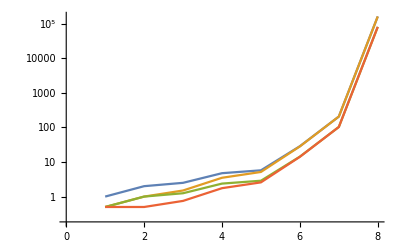

```mathematica
ListLogPlot[numslastest["orig"],Joined->True]
```

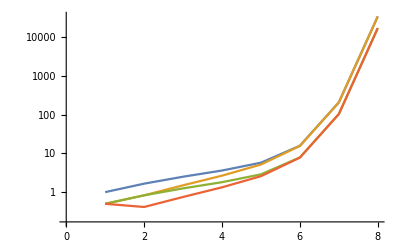

```mathematica
ListLogPlot[numslastest["smth"],Joined->True]
```

### Quasitrivial Semigroups

http://oeis.org/A292932 - Number of quasitrivial semigroups on an arbitrary n-element set. 
E.g.f.: 1/(x+3-2*exp(x)). -- exponential generating function
https://oeis.org/A292933 - E.g.f.: x/(x+3-2*exp(x)). -- with identity or with zero
https://oeis.org/A292934 - E.g.f.: x^2/(x+3-2*exp(x)).  -- with both identity and zero
Quasitrivial: a*b = one of a, b

N(“ident or zero”,n) = n*N(n-1)
N(“ident and zero”,n) = n*(n-1)*N(n-2)

https://arxiv.org/abs/1709.09162
Quasitrivial semigroups: characterizations and enumerations
Miguel Couceiro, Jimmy Devillet, Jean-Luc Marichal

Series base: 0

#### Data

```mathematica
numdata["smg qstv flip"] = {1,1,4,20,138,1182,12166,146050,2003882,30930734,530477310,10007736906,205965058162,4592120925862,110259944144486,2836517343551714,77836238876829882,2269379773783175454,70057736432648552782,2282895953541692345722};
```

```mathematica
numdata["smg qstv id flip"] = {0,1,2,12,80,690,7092,85162,1168400,18034938,309307340,5835250410,120092842872,2677545756106,64289692962068,1653899162167290,45384277496827424,1323216060906107994,40848835928097158172,1331096992220322502858};
```

```mathematica
numdata["smg qstv idzr flip"] = {0,0,2,6,48,400,4140,49644,681296,10515600,180349380,3402380740,70023004920,1561206957336,37485640585484,964345394431020,26462386594676640,771532717446066208,23817889096309943892,776127882633846005268};
```

#### Formulas

```mathematica
numvallist["smg qstv flip",nmax_?ispzint] := Module[{a},
a[0] = 1;
Do[a[n] = n*a[n-1] + 2*Sum[Binomial[n,k]*a[k],{k,0,n-2}],{n,nmax}];
Array[a,nmax+1,0]
]
```

```mathematica
numval["smg qstv flip",n_?ispzint] := Sum[2^i*(-1)^k*Binomial[n,k]*StirlingS2[n-k,i]*(i+k)!,{i,0,n},{k,0,n-i}]
```

```mathematica
numvallist["smg qstv flip gnf",nmax_?ispzint] := Block[{x},CoefficientList[Series[1/(3+x-2*Exp[x]),{x,0,nmax}],x]*Range[0,nmax]!]
```

```mathematica
(* Asymptotic formula *)
```

```mathematica
(* LambertW[-1,z] = ProductLog[z], solution for w in z = w*Exp[w] *)
```

```mathematica
nqtasc = - LambertW[-1,-2Exp[-3.]]
```

3.58307

```mathematica
numasymp["smg qstv flip",n_] := n!/((nqtasc-1)(nqtasc-3)^(n+1))
```

#### Tests

```mathematica
(# - numvallist["smg qstv flip",Length[#]-1])& @ numdata["smg qstv flip"] // Tally
```

{{0,20}}

```mathematica
shfmlt[shf_,data_] := Join[ConstantArray[0,shf],Table[Product[n+k,{k,0,shf-1}],{n,Length[data]}]*data]
```

```mathematica
(# - Take[shfmlt[1,numdata["smg qstv flip"]],Length[#]])& @ numdata["smg qstv id flip"] // Tally
```

{{0,20}}

```mathematica
(# - Take[shfmlt[2,numdata["smg qstv flip"]],Length[#]])& @ numdata["smg qstv idzr flip"] // Tally
```

{{0,20}}

### Simple Semigroups

From
Enumerating 0-simple semigroups
https://research-repository.st-andrews.ac.uk/handle/10023/23558

0-simple: Rees matrix semigroup
H-triv: with trivial group
w 0: no zero, with zero added on

Series base: 1

#### Data

```mathematica
numdata["smg smpl 0-smpl"] = {0,1,3,3,9,3,18,3,33,23,30,3,151,3,46,189,294,3,487,3,1397,664,90,3,5648,3841,118,1917,11716,3,45398,3,31996,4503,186,204185,285790,3,226,9706,1116191,3,3583160,3,399960,3881357,318,3,30271239,29610810,15214393,35305,1757051,3,222104344,55205944,922866288,61480,486,3,1762675631,3,550,13190856618,13718901762,625728729,10187010096,3,22657053,163155,176974898340,3,823881619734,3,766,5836761933,69496618,2146892812097,356407493734,3,19580066324253,20677459330076,930,3,26419833132046,46093054629,1018,552177,464292341808739,3,2094085011265979,260383999114719,514299114,789124,1206,315901054341,10256563628288892,3,2597046185315768,97100184784203210,103611007719055260,3,222670079940176,3,208703812193138857,24357579732335554,1518,3,4188448777559775907,3,19091741727581499836,2059390,4201290929266046145,3,4212693723851078,10412895280125,6565200607,167692379464165700555,1866,1814914300200409639,1700378443600053588142,1745061194503344181720,1990,3619077,13963742950,51505577788824,6275790700072159443717,3,1203342802955800797357,4708924};
```

```mathematica
numdata["smg smpl H-triv"] = {0,1,2,2,5,2,12,2,18,19,24,2,116,2,40,184,229,2,420,2,1338,658,84,2,5230,3837,112,1862,11618,2,44594,2,30710,4498,180,204180,282970,2,220,9700,1101448,2,3577908,2,399718,3879780,312,2,30156838,29610806,15069848,35300,1756696,2,222070638,55205938,922263078,61474,480,2,1757017984,2,544,13190836800,13715458490,625728724,10186888516,2,22656374,163150,176878810270,2,823708035742,2,760,5834602820,69495720,2146892812092,356407038668,2,19578467831806,20677459128734,924,2,26404057549872,46093054624,1012,552172,464291948898156,2,2094063283672984,260383999114714,514297640,789118,1200,315901054336,10255839996389954,2,2595854189959052,97100184782573478,103610729300331610,2,222670075515736,2,208703805552811252,24357568048361550,1512,2,4188419057295337524,2,19091738417871913466,2059384,4200967305301010852,2,4212693711897014,10412895280120,6565197868,167692379464154875548,1860,1814914300200409634,1700377301105413386160,1745061194503344181716,1984,3619072,13963739668,51505321476420,6275751281470592125364,2,1203277350014102636584,4708918};
```

```mathematica
numdata["smg smpl w 0"] = {0,1,3,3,7,3,10,3,17,7,10,3,29,3,10,9,46,3,32,3,31,10,10,3,102,7,10,22,32,3,56,3,166,9,10,9,178,3,10,10,153,3,78,3,36,83,10,3,661,7,80,9,39,3,305,10,260,10,10,3,1431,3,10,243,1543,9,122,3,43,9,552,3,5763,3,10,2889,44,9,162,3,14566,736,10,3,14646,9,10,9,923,3,67314,9,48,10,10,9,185084,3,8219,1817,278968,3,248,3,1765,654268,10,3,1177657,3,11944,10,1202115,3,312,9,55,4507,10,9,28032758,7,10,9,56,2759049,65212924,3,10195549,10};
```

```mathematica
numdata["smg smpl grp w 0"] = {0,1,1,1,2,1,2,1,5,2,2,1,5,1,2,1,14,1,5,1,5,2,2,1,15,2,2,5,4,1,4,1,51,1,2,1,14,1,2,2,14,1,6,1,4,2,2,1,52,2,5,1,5,1,15,2,13,2,2,1,13,1,2,4,267,1,4,1,5,1,4,1,50,1,2,3,4,1,6,1,52,15,2,1,15,1,2,1,12,1,10,1,4,2,2,1,231,1,5,2,16,1,4,1,14,2,2,1,45,1,6,2,43,1,6,1,5,4,2,1,47,2,2,1,4,5,16,1,2328,2};
```

#### Tests

```mathematica
(# - FiniteGroupCount[Range[Length[#]]])& @ Rest[numdata["smg smpl grp w 0"]] // Tally
```

{{0,129}}

### Monoids

Has associativity, an identity.

https://oeis.org/A058129 - Number of monoids (semigroups with identity) of order n.
https://oeis.org/A058133 - Number of monoids (semigroups with identity) of order n, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator). 
https://oeis.org/A058131 - Number of commutative monoids (commutative semigroups with identity) of order n. 
https://oeis.org/A058132 - Number of self-converse monoids (semigroups with identity) of order n.
http://oeis.org/A058154 - Number of labeled monoids of order n with a fixed identity. 
http://oeis.org/A058153 - Number of labeled monoids of order n. 
http://oeis.org/A058156 - Number of labeled commutative monoids of order n with a fixed identity.
http://oeis.org/A058155 - Number of labeled commutative monoids of order n. 

https://oeis.org/A234844 - Number of inverse monoids of order n. 
https://oeis.org/A234845 - Number of commutative inverse monoids of order n.
http://oeis.org/A151823 - Number of nonequivalent monoids of order n with more than one invertible element 
(group part is nontrivial)
http://oeis.org/A176142 - Number of nonequivalent monoids of order n in which the action of the unit group on the maximal ideal is nontrivial.

Series base: 1

#### Data

```mathematica
numdata["mnd"] = {1,2,7,35,228,2237,31559,1668997};
```

```mathematica
numdata["mnd flip"] = {1,2,6,27,156,1373,17730,858977,1844075697,52991253973742};
```

```mathematica
numdata["mnd cmt"] = {1,2,5,19,78,421,2637};
```

```mathematica
numdata["mnd scnv"] = {1,2,5,19,84,509,3901,48957};
```

```mathematica
numdata["mnd lbl ifx"] = {1,2,11,156,4122,208672,18507440,7892741602};
```

```mathematica
numdata["mnd lbl"] = {1,4,33,624,20610,1252032,129552080,63141932606};
```

```mathematica
numdata["mnd cmt lbl ifx"] = {1,2,9,94,1486,38890,1430442};
```

```mathematica
numdata["mnd cmt lbl"] = {1,4,27,376,7430,233340,10013094};
```

```mathematica
numdata["mnd inv flip"] = {1,2,4,11,27,89,310,1311,6253,34325,212247,1466180,11167987,92889294,836021796};
```

```mathematica
numdata["mnd inv cmt"] = {1,2,4,11,27,87,300,1259,5988,32812,202784,1400541,10669344,88761928,799112310};
```

```mathematica
numdata["mnd ntvgrp flip"] = {0,1,2,9,30,213,1757,22956,955569,1853259264};
```

```mathematica
numdata["mnd ntvact flip"] = {0,0,0,2,5,58,428,5539,101082,9269715};
```

#### Tests

```mathematica
(* Test formula for nontrivial group part *)
```

```mathematica
numdata["mnd flip"] - (Take[numdata["smg flip"],Length[numdata["mnd flip"]]]+ numdata["mnd ntvgrp flip"]) // Tally
```

{{0,10}}

```mathematica
(* Test formula for nontrivial group action on the semigroup part *)
```

```mathematica
numval["mnd tvlact flip",n_] := Sum[FiniteGroupCount[k]*numdata["smg flip"][[n-k+1]],{k,1,n}]
```

```mathematica
numdata["mnd flip"] - (numval["mnd tvlact flip",Range[Length[numdata["mnd flip"]]]] + numdata["mnd ntvact flip"]) // Tally
```

{{0,10}}

### Idempotent Monoids

With idempotents.

https://oeis.org/A058137 - Triangle read by rows: monoids of order n with k idempotents.
https://oeis.org/A058147 - Triangle read by rows: number of monoids of order n with k idempotents, considered to be equivalent when they are isomorphic or anti-isomorphic (by reversal of the operator).
https://oeis.org/A058142 - Triangle read by rows: number of commutative monoids of order n with k idempotents.
https://oeis.org/A058144 - Triangle: Self-converse monoids of order n with k idempotents.
http://oeis.org/A058158 - Triangle: Labeled monoids of order n with k idempotents with a fixed identity.
http://oeis.org/A058157 - Triangle: Labeled monoids of order n with k idempotents.
http://oeis.org/A058160 - Triangle: Labeled commutative monoids of order n with k idempotents with a fixed identity. 
http://oeis.org/A058159 - Triangle: Labeled commutative monoids of order n with k idempotents. 

For idempotent monoids, uses idempotent semigroups with sequence locations bumped up. This is because the monoids are (identity) + (idempotent semigroup)

http://oeis.org/A058164 - Number of labeled lattices with a fixed bottom.
http://oeis.org/A055512 - Lattices with n labeled elements.

Kleitman, D. J., & Winston, K. J. (1980). The Asymptotic Number of Lattices. Annals of Discrete Mathematics, 243–249. doi:10.1016/s0167-5060(08)70708-8

#### Data

```mathematica
numtridata["mnd idmp"] = maketri[{1,1,1,1,3,3,2,9,14,10,1,32,63,86,46,2,219,406,694,665,251,1,5585,3331,6343,8582,6035,1682}];
```

```mathematica
numtridata["mnd idmp flip"] = maketri[{1,1,1,1,3,2,2,9,10,6,1,30,47,52,26,2,175,283,413,365,135,1,3333,2139,3630,4597,3155,875}];
```

```mathematica
numtridata["mnd idmp cmt"] = maketri[{1,1,1,1,3,1,2,9,6,2,1,26,30,16,5,1,98,142,111,54,15,1,455,718,713,482,215,53}];
```

```mathematica
numtridata["mnd idmp scnv"] = maketri[{1,1,1,1,3,1,2,9,6,2,1,28,31,18,6,2,131,160,132,65,19,1,1081,947,917,612,275,68}];
```

```mathematica
numtridata["mnd idmp lbl ifx"] = maketri[{1, 1, 1, 1, 6, 4, 4, 45, 72, 35, 6, 528, 1308, 1676, 604, 80, 19935, 39700, 70170, 62060, 16727, 120, 3599436, 1969470, 3829000, 5167800, 3260382, 681232}];
```

```mathematica
numtridata["mnd idmp lbl"] = maketri[{1,2,2,3,18,12,16,180,288,140,30,2640,6540,8380,3020,480,119610,238200,421020,372360,100362,840,25196052,13786290,26803000,36174600,22822674,4768624}];
```

```mathematica
numtridata["mnd idmp cmt lbl ifx"] = maketri[{1,1,1,1,6,2,4,45,36,9,6,408,648,348,76,60,7195,13500,11790,5280,1065,120,200016,369930,425280,293640,118890,22566}];
```

```mathematica
numtridata["mnd idmp cmt lbl"] = maketri[{1,2,2,3,18,6,16,180,144,36,30,2040,3240,1740,380,360,43170,81000,70740,31680,6390,840,1400112,2589510,2976960,2055480,832230,157962}];
```

```mathematica
numdata["mnd idmp"] = Prepend[numdata["smg idmp"],1];
```

```mathematica
numdata["mnd idmp flip"] = Prepend[numdata["smg idmp flip"] ,1];
```

```mathematica
numdata["mnd idmp cmt"] = Prepend[numdata["smg idmp cmt"] ,1];
```

```mathematica
numdata["mnd idmp scnv"] = Prepend[numdata["smg idmp scnv"] ,1];
```

```mathematica
numdata["mnd idmp lbl ifx"] = Prepend[numdata["smg idmp lbl"] ,1];
```

```mathematica
numdata["mnd idmp lbl"] = identfixtognl[numdata["mnd idmp lbl ifx"] ];
```

```mathematica
numdata["mnd idmp cmt lbl ifx"] = Prepend[numdata["smg idmp cmt lbl"] ,1];
```

```mathematica
numdata["mnd idmp cmt lbl"] = identfixtognl[numdata["mnd idmp lbl cmt ifx"] ];
```

#### Tests

```mathematica
numtridata["mnd idmp lbl"] - identfixtognl[numtridata["mnd idmp lbl ifx"]] // Flatten // Tally
```

{{0,28}}

```mathematica
numtridata["mnd idmp cmt lbl"] - identfixtognl[ numtridata["mnd idmp cmt lbl ifx"]] // Flatten // Tally
```

{{0,28}}

### Groups

Has  associativity, an identity, and division (inverses).

https://oeis.org/A000001 - Number of groups of order n. 
https://oeis.org/A000688 - Number of Abelian groups of order n; number of factorizations of n into prime powers.
https://oeis.org/A058163 - Number of labeled groups with a fixed identity.
https://oeis.org/A034383 - Number of labeled groups. 
https://oeis.org/A058162 - Number of labeled Abelian groups with a fixed identity.
https://oeis.org/A034382 - Number of labeled Abelian groups of order n.
https://oeis.org/A058161 - Number of labeled cyclic groups with a fixed identity.
https://oeis.org/A034381 - Number of labeled cyclic groups. 
https://oeis.org/A066060 - Number of nilpotent groups of order n. 

[math/0605185] Automorphisms of finite Abelian groups
Christopher J. Hillar, Darren Rhea
https://arxiv.org/abs/math/0605185

https://oeis.org/A021002 - Decimal expansion of zeta(2)*zeta(3)*zeta(4)*... 
Asymptotic value of the mean number of abelian groups below some order

Series base: 1

#### Data

```mathematica
numdata["grp"] = {1,1,1,2,1,2,1,5,2,2,1,5,1,2,1,14,1,5,1,5,2,2,1,15,2,2,5,4,1,4,1,51,1,2,1,14,1,2,2,14,1,6,1,4,2,2,1,52,2,5,1,5,1,15,2,13,2,2,1,13,1,2,4,267,1,4,1,5,1,4,1,50,1,2,3,4,1,6,1,52,15,2,1,15,1,2,1,12,1,10,1,4,2};
```

```mathematica
numdata["grp cmt"] = {1,1,1,2,1,1,1,3,2,1,1,2,1,1,1,5,1,2,1,2,1,1,1,3,2,1,3,2,1,1,1,7,1,1,1,4,1,1,1,3,1,1,1,2,2,1,1,5,2,2,1,2,1,3,1,3,1,1,1,2,1,1,2,11,1,1,1,2,1,1,1,6,1,1,2,2,1,1,1,5,5,1,1,2,1,1,1,3,1,2,1,2,1,1,1,7,1,2,2,4,1,1,1,3,1,1,1};
```

```mathematica
numdata["grp lbl ifx"] = {1,1,1,4,6,80,120,2760,7560,108864,362880,21621600,39916800,1186099200,10897286400,647091244800,1307674368000,103742166528000,355687428096000,32438693442355200,260668072304640000,5573557327822848000,51090942171709440000};
```

```mathematica
numdata["grp lbl"] = {1,2,3,16,30,480,840,22080,68040,1088640,3991680,259459200,518918400,16605388800,163459296000,10353459916800,22230464256000,1867358997504000,6758061133824000,648773868847104000,5474029518397440000,122618261212102656000};
```

```mathematica
numdata["grp cmt lbl ifx"] = {1,1,1,4,6,60,120,1920,7560,90720,362880,13305600,39916800,1037836800,10897286400,265686220800,1307674368000,66691392768000,355687428096000,20274183401472000,202741834014720000};
```

```mathematica
numdata["grp cmt lbl"] = {1,2,3,16,30,360,840,15360,68040,907200,3991680,159667200,518918400,14529715200,163459296000,4250979532800,22230464256000,1200445069824000,6758061133824000,405483668029440000};
```

```mathematica
numdata["grp cyc lbl ifx"] = {1,1,1,3,6,60,120,1260,6720,90720,362880,9979200,39916800,1037836800,10897286400,163459296000,1307674368000,59281238016000,355687428096000,15205637551104000,202741834014720000,5109094217170944000,51090942171709440000};
```

```mathematica
numdata["grp cyc lbl"] = {1,2,3,12,30,360,840,10080,60480,907200,3991680,119750400,518918400,14529715200,163459296000,2615348736000,22230464256000,1067062284288000,6758061133824000,304112751022080000};
```

```mathematica
numdata["grp nil"] = {1,1,1,2,1,1,1,5,2,1,1,2,1,1,1,14,1,2,1,2,1,1,1,5,2,1,5,2,1,1,1,51,1,1,1,4,1,1,1,5,1,1,1,2,2,1,1,14,2,2,1,2,1,5,1,5,1,1,1,2,1,1,2,267,1,1,1,2,1,1,1,10,1,1,2,2,1,1,1,14,15,1,1,2,1,1,1,5,1,2,1,2,1,1,1,51,1,2,2,4,1};
```

#### Built-In, Abelian (Commutative), and Nilpotent Formulas

```mathematica
(* Check against built-in *)
```

```mathematica
numval["grp",n_?isposint] := FiniteGroupCount[n]
```

```mathematica
numval["grp cmt",n_?isposint] := FiniteAbelianGroupCount[n]
```

```mathematica
(* One cyclic group per order *)
```

```mathematica
numval["grp cyc",n___] := 1
```

```mathematica
(* Check abelian-group formulas *)
```

```mathematica
(* From OEIS: Times @@ PartitionsP /@ Last /@ FactorInteger @ n *)
```

```mathematica
numval["grp cmt x",n_?isposint] := PrimePowerFunc[n,PartitionsP[#2]&]
```

```mathematica
numval["grp ppcyc",n_?isposint] := If[n>1,Boole[PrimePowerQ[n]],1]
```

```mathematica
numval["grp ppcyc x",n_?isposint] := If[Length[FactorInteger[n]]==1,1,0]
```

```mathematica
(* Check nilpotent-group formula - is every nilpotent group the product of distinct-prime p-groups? *)
```

```mathematica
numval["grp nil",n_?isposint] := PrimePowerFunc[n,FiniteGroupCount[#1^#2]&]
```

```mathematica
(* Number of automorphisms of abelian groups with some set of prime powers *)
```

```mathematica
numamcg[p_,pwrs_List] := Module[{psrt,n,ixtab,ixmin,ixmax},
psrt = Sort[pwrs];
n = Length[pwrs];
ixtab = Table[Select[Range[n],psrt[[#]]==psrt[[k]]&],{k,n}];
ixmin = Min /@ ixtab; ixmax = Max /@ ixtab;
Product[(p^ixmax[[k]]-p^(k-1))*p^(psrt[[k]]*(n-ixmax[[k]]) + (psrt[[k]]-1)*(n-ixmin[[k]]+1)),{k,n}]
]
```

```mathematica
numval["grp cmt lbl ifx",n_?isposint] := (n-1)!*PrimePowerFunc[n,Sum[1/numamcg[#1,pt],{pt,IntegerPartitions[#2]}]&]
```

```mathematica
numval["grp cmt lbl",n_?isposint] := n*numval["grp cmt lbl ifx",n]
```

```mathematica
numval["grp cyc lbl ifx",n_?isposint] := (n-1)!/EulerPhi[n]
```

```mathematica
numval["grp cyc lbl",n_?isposint] := n*numval["grp cyc lbl ifx",n]
```

```mathematica
(* Asymptotic value of the average number of abelian groups per order *)
```

```mathematica
ncmtgasymp = Product[Zeta[N[n]],{n,2,100}]
```

2.29486

```mathematica
numasymp["grp cmt",n___] := ncmtgasymp
```

#### Prime Powers (p-groups)

```mathematica
(* Mathematica has powers of 2 up to 10, all other prime powers up to 7 *)
```

```mathematica
numval["grp prmpwr",p_?PrimeQ,0] := 1
```

```mathematica
numval["grp prmpwr",p_?PrimeQ,1] := 1
```

```mathematica
numval["grp prmpwr",p_?PrimeQ,2] :=2
```

```mathematica
numval["grp prmpwr",p_?PrimeQ,3] :=5
```

```mathematica
numval["grp prmpwr",p_?PrimeQ,4] :=Which[p==2,14,True,15]
```

```mathematica
numval["grp prmpwr",p_?PrimeQ,5] :=Which[p==2,51,p==3,67,True,2p+61 + 2GCD[p-1,3] + GCD[p-1,4]]
```

```mathematica
numval["grp prmpwr",p_?PrimeQ,6] :=Which[p==2,267,p==3,504,True,3p^2+39*p+344 + 24GCD[p-1,3] + 11GCD[p-1,4] + 2GCD[p-1,5]]
```

```mathematica
numval["grp prmpwr",p_?PrimeQ,7] :=Which[p==2,2328,p==3,9310,p==5,34297,True,3p^5+12p^4+44p^3+170p^2+707p+2455 + (4p^2+44p+291)GCD[p-1,3] + (p^2+19p+135)GCD[p-1,4] + (3p+31)GCD[p-1,5]+ 4GCD[p-1,7]+5GCD[p-1,8]+GCD[p-1,9]]
```

```mathematica
numval["grp ppird",p_?PrimeQ,0] :=1
```

```mathematica
numval["grp ppird",p_?PrimeQ,1] :=1
```

```mathematica
numval["grp ppird",p_?PrimeQ,2] :=1
```

```mathematica
numval["grp ppird",p_?PrimeQ,3] :=3
```

```mathematica
numval["grp ppird",p_?PrimeQ,4] :=Which[p==2,8,True,9]
```

```mathematica
numval["grp ppird",p_?PrimeQ,5] :=Which[p==2,34,p==3,49,True,2p +43 + 2GCD[p-1,3]+GCD[p-1,4]]
```

```mathematica
numval["grp ppird",p_?PrimeQ,6] :=Which[p==2,201,p==3,421,True,3p^2+37*p+267 + 22GCD[p-1,3] + 10GCD[p-1,4]+2GCD[p-1,5]]
```

```mathematica
numval["grp ppird",p_?PrimeQ,7] :=Which[p==2,2000,p==3,8727,p==5,33524,True,3p^5+12p^4+44p^3+167p^2+666p+2038 + (4p^2+44p+265)GCD[p-1,3] + (p^2+19p+123)GCD[p-1,4] + (3p+29)GCD[p-1,5]+ 4GCD[p-1,7]+5GCD[p-1,8]+GCD[p-1,9]]
```

```mathematica
testppgrp[n_Integer] := Table[Table[numval["grp prmpwr",p,m]-numval["grp",p^m],{m,7}],{p,Prime[Range[n]]}] // Tally
```

```mathematica
testppgrp[100]
```

{{{0,0,0,0,0,0,0},100}}

```mathematica
testppirdgrp[n_Integer] := Table[numval["grp ppird",p,Range[7]] - PartIrredArray[numval["grp prmpwr",p,Range[7]]],{p,Prime[Range[n]]}] // Tally
```

```mathematica
testppirdgrp[100]
```

{{{0,0,0,0,0,0,0},100}}

#### Multiple Primes in Group Order

```mathematica
areallprime[plst_] := And @@ (PrimeQ /@ plst)
```

```mathematica
(* Total f[p*q] = Irreducible f[p*q] + f[p]*f[q] *)
```

```mathematica
numgrp["p11",prms_] := Module[{p,q},
If[!areallprime[prms],Return[]];
{p,q} = Sort[prms];
If[q == p,Return[numval["grp prmpwr",p,2]]];
If[Mod[q-1,p]==0,2,1]
]
```

```mathematica
numgrp["p11 ird",prms_] := Module[{p,q},
If[!areallprime[prms],Return[]];
{p,q} = Sort[prms];
If[q == p,Return[numval["grp ppird",p,2]]];
If[Mod[q-1,p]==0,1,0]
]
```

```mathematica
numgrptest["p11",pnmax_] := Flatten[Table[numgrp["p11",{p,q}] - {FiniteGroupCount[p*q],numgrp["p11 ird",{p,q}]+1},{p,Prime[Range[pnmax]]},{q,Prime[Range[pnmax]]}],1] // Tally
```

```mathematica
(* Total f[p*q^2] = Irreducible f[p*q^2] + f[p]*f[q^2] + f[p*q]*f[q] + f[p]*f[q]^2 if q ≠ p, f[p^3] + f[p]*f[p^2] + f[p]^3 if q == p *)
```

```mathematica
numgrp["p12",prms_] := Module[{p,q},
If[!areallprime[prms],Return[]];
{p,q} = prms;
If[q == p,Return[numval["grp prmpwr",p,3]]];
Which[p==2,5,p>2 && Mod[q-1,p]==0,(p+9)/2,p==3&&q==2,5,p>2 && q>2 && Mod[q+1,p]==0,3,p>3 && Mod[p-1,q]==0 && Mod[p-1,q^2]≠0,4,Mod[p-1,q^2]==0,5,Mod[q-1,p]≠0 && Mod[q+1,p]≠0 && Mod[p-1,q]≠0,2]
]
```

```mathematica
numgrp["p12 ird",prms_] := Module[{p,q},
If[!areallprime[prms],Return[]];
{p,q} = prms;
If[q == p,Return[numval["grp ppird",p,3]]];
Which[p==2,2,p>2 && Mod[q-1,p]==0,(p+3)/2,p==3&&q==2,2,p>2 && q>2 && Mod[q+1,p]==0,1,p>3 && Mod[p-1,q]==0 && Mod[p-1,q^2]≠0,1,Mod[p-1,q^2]==0,2,Mod[q-1,p]≠0 && Mod[q+1,p]≠0 && Mod[p-1,q]≠0,0]
]
```

```mathematica
numgrptest["p12",pnmax_] := Flatten[Table[numgrp["p12",{p,q}] - {FiniteGroupCount[p*q^2],numgrp["p12 ird",{p,q}]+ If[q≠p,numgrp["p11 ird",{p,q}],0] + numval["grp ppird",q,2] + 1},{p,Prime[Range[pnmax]]},{q,Prime[Range[pnmax]]}],1] // Tally
```

```mathematica
(* Total f[p*q*r] = Irreducible f[p*q*r] + f[p]*f[q*r] + f[q]*f[p*r] + f[r]*f[p*q] + f[p]*f[q]*f[r] if p,q,r all different, f[p*q^2] + f[p]*f[q^2] + f[q]*f[p*q] + f[p]*f[q]^2 if p ≠ q == r and likewise for appropriate permutations and f[p^3] + f[p]*f[p^2] + f[p]^3 for all equal *)
```

```mathematica
numgrp["p111",prms_] := Module[{psrt,p,q,r,cqp,crp,crq},
If[!areallprime[prms],Return[]];
psrt = Sort[prms];
{p,q,r} = psrt;
If[q == p && r == p,Return[numval["grp prmpwr",p,3]]];
If[q == p,Return[numgrp["p12",{r,p}]]];
If[r == p,Return[numgrp["p12",{q,p}]]];
If[r == q,Return[numgrp["p12",{p,q}]]];
cqp = Mod[q-1,p]==0; crp = Mod[r-1,p]==0; crq = Mod[r-1,q]==0;
If[cqp,If[crp,If[crq,p+4,p+2],If[crq,3,2]],If[crp,If[crq,4,2],If[crq,2,1]]]
]
```

```mathematica
numgrp["p111 ird",prms_] := Module[{psrt,p,q,r,cqp,crp,crq},
If[!areallprime[prms],Return[]];
psrt = Sort[prms];
{p,q,r} = psrt;
If[q == p && r == p,Return[numval["grp ppird",p,3]]];
If[q == p,Return[numgrp["p12 ird",{r,p}]]];
If[r == p,Return[numgrp["p12 ird",{q,p}]]];
If[r == q,Return[numgrp["p12 ird",{p,q}]]];
cqp = Mod[q-1,p]==0; crp = Mod[r-1,p]==0; crq = Mod[r-1,q]==0;
If[crp,If[cqp,p-1,0]+If[crq,1,0],0]
]
```

```mathematica
numgrptest["p111",pnmax_] := Flatten[Table[numgrp["p111",{p,q,r}] - {FiniteGroupCount[p*q*r],numgrp["p111 ird",{p,q,r}] + Which[p==q&&p==r,numval["grp ppird",p,2],q==r,numval["grp ppird",q,2] + numgrp["p11 ird",{p,q}],p==r,numval["grp ppird",p,2] + numgrp["p11 ird",{p,q}],p==q,numval["grp ppird",p,2] + numgrp["p11 ird",{p,r}],True,numgrp["p11 ird",{p,q}]+ numgrp["p11 ird",{p,r}]+numgrp["p11 ird",{q,r}]]+ 1},{p,Prime[Range[pnmax]]},{q,Prime[Range[pnmax]]},{r,Prime[Range[pnmax]]}],2] // Tally
```

#### Tests

```mathematica
(# - numval["grp",Range[Length[#]]])& @ numdata["grp"] // Tally
```

{{0,93}}

```mathematica
(# - numval["grp cmt",Range[Length[#]]])& @ numdata["grp cmt"] // Tally
```

{{0,107}}

```mathematica
testcmtgrp[n_?isposint] := (numval["grp cmt x",#] - numval["grp cmt",#])& @ Range[n]
```

```mathematica
testcmptgrpprmpwr[n_?isposint] := (numval["grp ppcyc x",#] -numval["grp ppcyc",#])& @ Range[n]
```

```mathematica
testcmtgrpreduce[n_?isposint] := (numval["grp ppcyc",#] - DivisorIrredArray[numval["grp cmt",#]])& @ Range[n]
```

```mathematica
testcmtgrp[1000] // Tally
```

{{0,1000}}

```mathematica
testcmptgrpprmpwr[1000] // Tally
```

{{0,1000}}

```mathematica
testcmtgrpreduce[100] // Tally
```

{{0,100}}

```mathematica
numtest["grp nil",1] // Tally
```

{{0,101}}

```mathematica
numtest["grp cmt lbl ifx",1] // Tally
```

{{0,21}}

```mathematica
numtest["grp cmt lbl",1] // Tally
```

{{0,20}}

```mathematica
numtest["grp cyc lbl ifx",1] // Tally
```

{{0,23}}

```mathematica
numtest["grp cyc lbl",1] // Tally
```

{{0,20}}

## Graphs

```mathematica
makepos[xlst_] := Max[#,1]& /@ xlst
```

```mathematica
shownums[lbls_] := ListLogPlot[makepos[numdata[#]]& /@ lbls,Joined->True,PlotRange->All,PlotLegends->lbls]
```

```mathematica
sncmt[lbl_] := shownums[{lbl,lbl<>" cmt"}]
```

```mathematica
sncmtlbl[lbl_] := shownums[{lbl<>" lbl",lbl<>" cmt lbl",lbl,lbl<>" cmt"}]
```

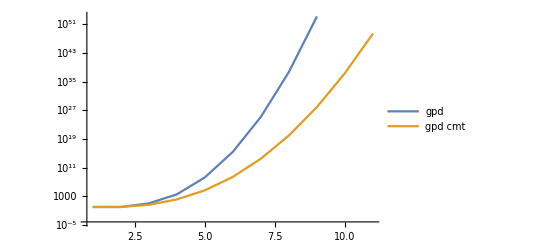
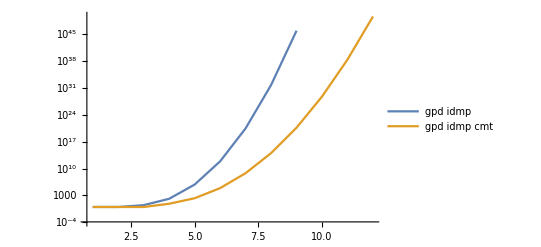
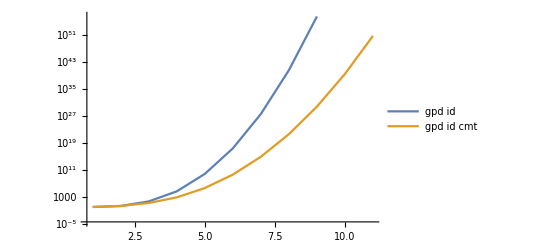
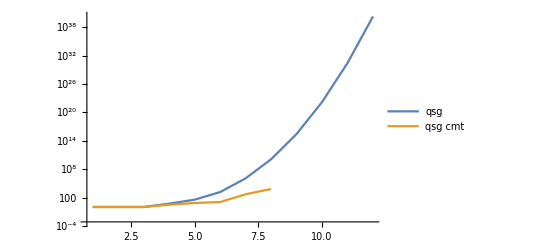
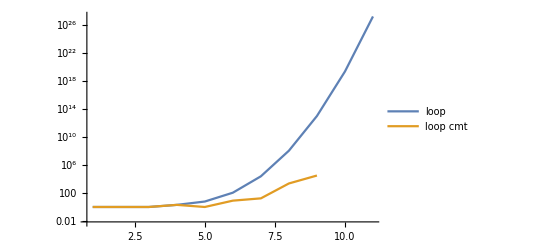
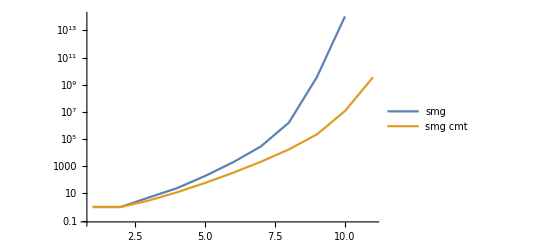
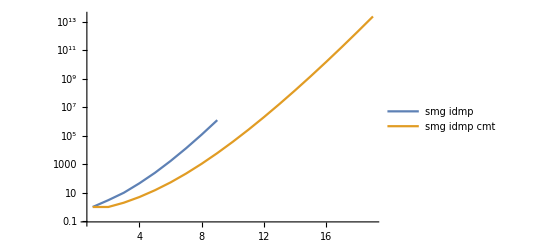
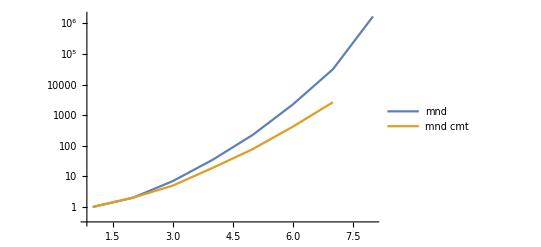

```mathematica
sncmt /@ {"gpd","gpd idmp","gpd id","qsg","loop","smg","smg idmp","mnd","mnd idmp"}
```

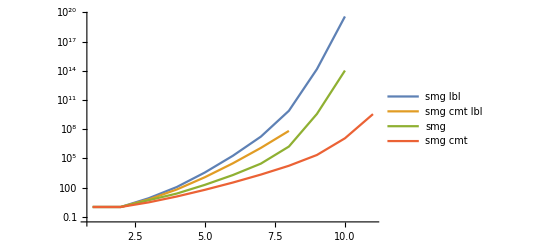
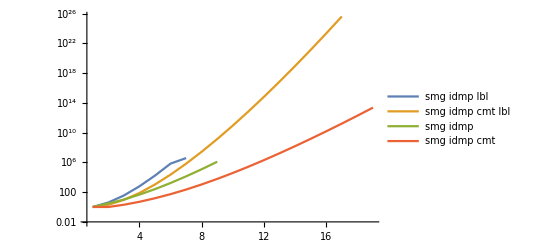
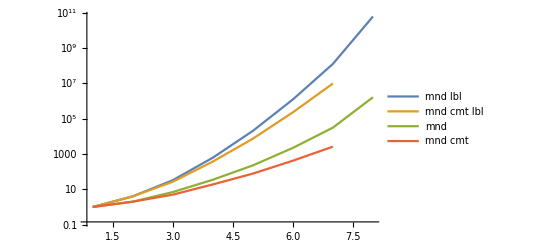
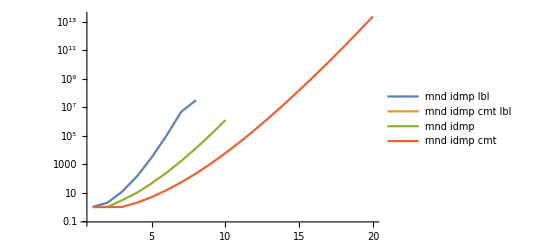

```mathematica
sncmtlbl /@ {"smg","smg idmp","mnd","mnd idmp"}
```

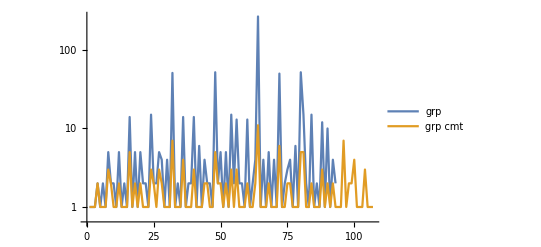

```mathematica
shownums[{"grp","grp cmt"}]
```

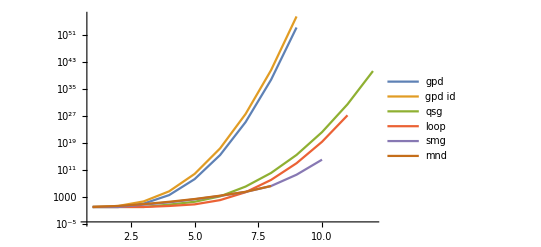

```mathematica
shownums[{"gpd","gpd id","qsg","loop","smg","mnd"}]
```

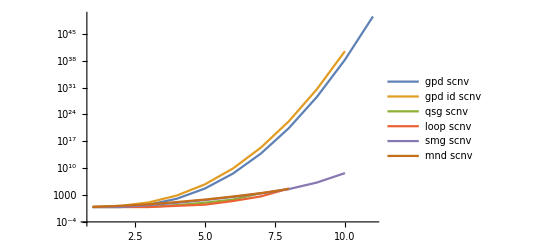

```mathematica
shownums[{"gpd scnv","gpd id scnv","qsg scnv","loop scnv","smg scnv","mnd scnv"}]
```

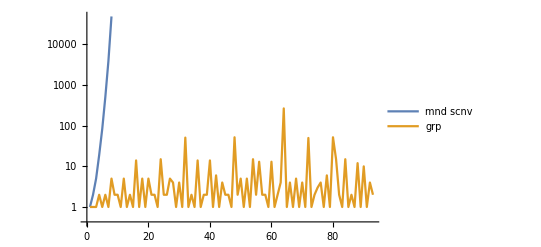

```mathematica
shownums[{"mnd scnv","grp"}]
```

## Estimated Asymptotic Behavior

### Factorial scaling between numbers for labeled and isomorphic algebras

```mathematica
(* Factorial scaling between labeled and isomorphic numbers? *)
```

```mathematica
facscldata[lbl_,nbase_] := Module[{lbld,isom,mnlen},
lbld = numdata[lbl <> " lbl"];
isom = numdata[lbl];
mnlen = Min[Length[lbld],Length[isom]];
lbld = Take[lbld,mnlen];
isom = Take[isom,mnlen];
(isom*((Range[mnlen]-1+nbase)!) - lbld)/N[lbld]
]
```

```mathematica
facsclval[lbl_,nbase_,nmax_] := Table[(numval[lbl,n]*n! - #)/N[#]& @ numval[lbl<>" lbl",n],{n,nbase,nmax}]
```

```mathematica
facsclval["gpd",0,10]
```

{0.,0.,0.25,0.0150892,0.000139594,2.70363×10^-7,3.78021×10^-10,3.37165×10^-13,2.0235×10^-16,8.71652×10^-20,2.8247×10^-23}

```mathematica
facsclval["gpd cmt",0,10]
```

{0.,0.,0.,0.0617284,0.00634766,0.000459076,0.0000224226,8.20008×10^-7,2.38172×10^-8,5.71707×10^-10,1.16827×10^-11}

```mathematica
facsclval["gpd idmp",1,10]
```

{0.,0.5,0.135802,0.00234222,7.52231×10^-6,1.15678×10^-8,1.26941×10^-11,9.09549×10^-15,4.55614×10^-18,1.68365×10^-21}

```mathematica
facsclval["gpd idmp cmt",1,10]
```

{0.,0.,0.555556,0.125,0.0119782,0.000717069,0.0000311348,1.07133×10^-6,2.98843×10^-8,6.96342×10^-10}

```mathematica
facsclval["gpd id",1,10]
```

{0.,0.,0.111111,0.00634766,0.0000577987,1.57184×10^-7,2.43871×10^-10,2.2997×10^-13,1.44066×10^-16,6.42261×10^-20}

```mathematica
facsclval["gpd id cmt",1,10]
```

{0.,0.,0.111111,0.0546875,0.00663296,0.000465077,0.000022158,8.03294×10^-7,2.32431×10^-8,5.57074×10^-10}

```mathematica
facscldata["qsg",0]
```

{0.,0.,0.,1.5,0.458333,0.0498512,0.00139155,0.0000129719,2.45852×10^-8,1.04653×10^-11,5.27961×10^-16,8.95735×10^-21}

```mathematica
facscldata["loop",1]
```

{0.,0.,1.,2.,1.57143,0.390306,0.00915118,0.00020923,3.39818×10^-7,4.78143×10^-10}

```mathematica
facscldata["smg",0]
```

{0.,0.,0.25,0.274336,0.292096,0.250735,0.20839,0.0594611,0.00232638,0.000259988}

```mathematica
facscldata["smg cmt",0]
```

{0.,0.,0.,0.142857,0.221053,0.269118,0.301997,0.313177}

```mathematica
facscldata["smg idmp",1]
```

{0.,0.5,0.714286,0.827815,0.800682,0.77772,16.4387}

```mathematica
facscldata["smg idmp cmt",1]
```

{0.,0.,0.333333,0.578947,0.690141,0.69104,0.658556,0.608628,0.560476,0.520208,0.487597,0.461866,0.441649,0.425735,0.413146,0.403133,0.395134}

```mathematica
facsclval["smg nil3",3,10]
```

{0.,0.2,0.208191,0.0886526,0.0174736,0.0019296,0.000259009,0.0000384676}

```mathematica
facsclval["smg nil3 cmt",3,10]
```

{0.,0.428571,0.703704,0.661456,0.386499,0.167447,0.0678149,0.0261778}

```mathematica
facscldata["slt",0]
```

{0.,0.,0.428571,0.868852,0.780645,0.270021,0.0263151,0.000355935}

```mathematica
facscldata["slt noid",0]
```

{0.,0.,0.5,0.866667,0.743725,0.264904,0.026288,0.000355934}

```mathematica
facscldata["slt nozr",0]
```

{0.,0.,0.428571,0.868852,0.780645,0.270021,0.0263151,0.000355935}

```mathematica
facscldata["slt noidzr",0]
```

{0.,0.,0.5,0.866667,0.743725,0.264904,0.026288,0.000355934}

```mathematica
facscldata["mnd",1]
```

{0.,0.,0.272727,0.346154,0.327511,0.286421,0.227748,0.065757}

```mathematica
facscldata["mnd cmt",1]
```

{0.,0.,0.111111,0.212766,0.259758,0.299049,0.32731}

```mathematica
facscldata["mnd idmp",1]
```

{0.,0.,0.5,0.714286,0.827815,0.800682,0.77772,16.4387}

```mathematica
facscldata["mnd idmp cmt",1]
```

{(1-numdata[mnd idmp lbl cmt ifx])/numdata[mnd idmp lbl cmt ifx]}

### Scaling of Latin squares, quasigroups, and loops

```mathematica
(* Number of Latin squares with size ≥ 1 *)
```

```mathematica
numlatsq = N[Rest[numdata["qsg lbl"]]];
```

```mathematica
nlsfct = N[Range[Length[numlatsq]]!];
```

```mathematica
(* isomorphism classes *)
```

```mathematica
Rest[numdata["qsg"]]/(numlatsq/nlsfct)
```

{1.,1.,2.5,1.45833,1.04985,1.00139,1.00001,1.,1.,1.,1.}

```mathematica
(* isotopy classes -- separate row, column, symbol interchange *)
```

```mathematica
numdata["loop lbl rcspm"]/(numlatsq/nlsfct^3)
```

{1.,4.,18.,48.,21.4286,10.102,1.17447,1.01012,1.00001,1.,1.}

```mathematica
(* isotopy with transpose *)
```

```mathematica
numdata["loop lbl rcstppm"]/(numlatsq/(2*nlsfct^3))
```

{2.,8.,36.,96.,42.8571,15.6122,1.34939,1.01505,1.00003,1.,1.}

```mathematica
(* main classes -- interchange between rows, columns, symbols *)
```

```mathematica
numdata["loop lbl rcsallpm"]/(numlatsq/(6*nlsfct^3))
```

{6.,24.,108.,288.,128.571,33.0612,1.83667,1.02559,1.00007,1.,1.}

### Labeled nilpotent degree-3 semigroups

```mathematica
(* For Latin squares, quasigroups, loops, semigroups, monoids, and groups in general, there is too little to go on *)
```

```mathematica
numval["smg nil3 lbl num",n_?ispzint] := If[n>0,Sum[Binomial[n,m]*m*Sum[(-1)^k*Binomial[m-1,k]*(m-k)^N[(n-m)^2],{k,0,m-1}],{m,2,Floor[n+1/2-Sqrt[n-3/4]]}],0]
```

```mathematica
numval["smg nil3 cmt lbl num",n_?ispzint] := If[n>0,Sum[Binomial[n,m]*m*Sum[(-1)^k*Binomial[m-1,k]*(m-k)^N[(n-m)*(n-m+1)/2],{k,0,m-1}],{m,2,Floor[n+3/2-Sqrt[2n+1/4]]}],0]
```

```mathematica
numval["smg nil3 lbl nmtest",n_?ispzint] := numval["smg nil3 lbl num",n]/(n^((1/2)n^2))
```

```mathematica
numval["smg nil3 cmt lbl nmtest",n_?ispzint] := numval["smg nil3 cmt lbl num",n]/(n^((1/4)n^2))
```

```mathematica
Log[numval["smg nil3 lbl num",Range[100]]]/Log[Range[100]]
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,-∞,1.63093,3.74593,5.82132,8.34009,11.5656,15.6887,20.5238,25.9548,32.0013,38.9047,46.8917,55.6737,65.1206,75.2155,86.007,97.8613,110.863,124.638,139.118,154.291,170.175,187.06,205.262,224.315825222098689,244.112768913022455,264.642543497308798,285.900897287863653,307.945857647682549,331.2934704475302234,355.8178091753118924,381.1371127943494513,407.2222725158160061,434.0674840582073625,461.6696627598113738,490.1001494756548439,519.9416153527517516,550.9279223238075115,582.7204959866320899,615.3014895848915843,648.6663160049361671,682.8114523435389288,717.7691058548013755,754.0703413834193007,791.6695653517429091,830.1038170732360576,869.346782399416714,909.3944635692485049,950.243349543429947,991.8957795616198065,1034.602160756427421,1078.883224605964165,1124.097199986510189,1170.138913136191093,1217.003836703231176,1264.688832305576292,1313.191169308574905,1362.533534143592717,1413.262582550307943,1465.356489959400012,1518.31202975955317,1572.107429600824129,1626.739762745899552,1682.20633330901745,1738.505060797253578,1795.687520118921894,1854.433606587325707,1914.39546258068071,1975.218503745993166,2036.893664339817821,2099.418471738639129,2162.790555087036696,2227.008068842291064,2292.124567666995271,2358.845571946183941,2426.775878722221558,2495.577124135116788,2565.2419759255415464,2635.7682424806326409,2707.153805587630377,2779.3967796403291744,2852.5228306430174853,2927.1701889227257688,3003.1618836038723122,3080.0390450789933962,3157.7905274237762278,3236.4143358066726439,3315.9085561978055379,3396.2713445279994905,3477.5069130601910719,3560.0123351566467934,3644.1303160424166169,3729.1703451295093804,3815.0947893455879506,3901.9017031091182109,3989.5893406664824002,4078.1559885963207468,4167.6005350610831313,4258.0191094506116131}

```mathematica
Differences[%]
```

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

{Indeterminate,∞,2.115,2.07539,2.51877,3.22553,4.12312,4.83505,5.43101,6.04651,6.90336,7.98698,8.78203,9.44694,10.0949,10.7915,11.8543,13.0013,13.7754,14.4796,15.1737,15.8833,16.885,18.2025,19.0537,19.796943690923766,20.529774584286343,21.258353790554855,22.044960359818896,23.347612799847674,24.524338727781669,25.319303619037559,26.085159721466555,26.845211542391356,27.602178701604011,28.43048671584347,29.841465877096908,30.98630697105576,31.792573662824578,32.580993598259494,33.364826420044583,34.145136338602762,34.957653511262447,36.301235528617925,37.599223968323608,38.434251721493149,39.242965326180656,40.047681169831791,40.848885974181442,41.652430018189859,42.706381194807615,44.281063849536744,45.213975380546024,46.041713149680904,46.864923567040083,47.684995602345117,48.502337002998612,49.342364835017813,50.729048406715226,52.093907409092069,52.955539800153158,53.795399841270959,54.632333145075423,55.466570563117898,56.2987274882361286,57.1824593216683151,58.7460864684038138,59.9618559933550031,60.8230411653124558,61.6751605938246544,62.5248073988213086,63.3720833483975664,64.2175137552543685,65.116498824704207,66.7210042791886694,67.930306776037618,68.8012454128952297,69.6648517904247583,70.5262665550910945,71.3855631069977361,72.2429740526987974,73.1260510026883108,74.6473582797082835,75.9916946811465434,76.877161475121084,77.7514823447828316,78.6238083828964161,79.494220391132894,80.3627883301939526,81.2355685321915814,82.5054220964557215,84.1179808857698236,85.0400290870927635,85.9244442160785702,86.8069137635302603,87.6876375573641893,88.5666479298383466,89.4445464647623845,90.4185743895284818}

```mathematica
Differences[%]
```

{Indeterminate,-∞,-0.039604,0.44338,0.706757,0.897589,0.711934,0.595955,0.615501,0.856856,1.08362,0.795045,0.664909,0.647969,0.696588,1.06279,1.14704,0.774056,0.704273,0.694034,0.709572,1.00172,1.31755,0.851209,0.743205,0.732830893362577,0.728579206268512,0.786606569264041,1.30265244002878,1.17672592793399,0.79496489125589,0.765856102428996,0.760051820924802,0.756967159212655,0.828308014239459,1.410979161253438,1.14484109395885,0.806266691768818,0.788419935434916,0.783832821785088,0.780309918558179,0.812517172659685,1.343582017355478,1.297988439705683,0.83502775316954,0.808713604687508,0.804715843651135,0.801204804349651,0.803544044008417,1.05395117661776,1.574682654729129,0.93291153100928,0.827737769134879,0.82321041735918,0.820072035305034,0.817341400653496,0.8400278320192,1.386683571697413,1.364859002376843,0.861632391061089,0.839860041117801,0.836933303804464,0.834237418042475,0.832156925118231,0.883731833432186,1.563627146735499,1.215769524951189,0.861185171957453,0.852119428512199,0.849646804996654,0.847275949576258,0.845430406856802,0.898985069449838,1.604505454484462,1.209302496848949,0.870938636857612,0.863606377529529,0.861414764666336,0.859296551906642,0.857410945701061,0.883076949989513,1.521307277019973,1.34433640143826,0.885466793974541,0.874320869661748,0.872326038113585,0.870412008236478,0.868567939061059,0.872780201997629,1.26985356426414,1.612558789314102,0.92204820132294,0.884415128985807,0.88246954745169,0.880723793833929,0.879010372474157,0.877898534924038,0.9740279247660973}

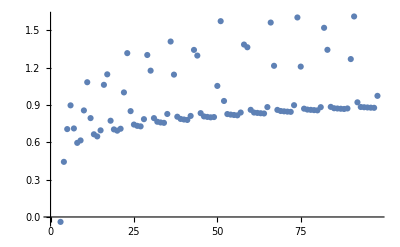

```mathematica
ListPlot[%]
```

```mathematica
Log[numval["smg nil3 cmt lbl num",Range[100]]]/Log[Range[100]]
```

Power::infy: Infinite expression 1/0 encountered.

{ComplexInfinity,-∞,1.63093,3.19616,4.59178,6.20339,8.14576,10.4545,13.1016,16.0771,19.4273,23.2201,27.4502,32.0572,37.0128,42.3404,48.1178,54.4003,61.128,68.2349,75.7027,83.5525,91.8671,100.731,110.08,119.829,129.953,140.455,151.379,162.847,174.886,187.378,200.266,213.537822787504358,227.200452527722669,241.306547043173249,255.995072226441558,271.268613012164656,286.994425317308133,303.1230071950784045,319.6458597431569158,336.5665166480982915,353.923677213570205,371.8588998768497086,390.4202554086200054,409.4588434301751085,428.9118934838055195,448.7689695334570048,469.0296995066139815,489.7100538518647908,510.9093179889340574,532.7750820319805463,555.1863632899523139,578.0321923107305701,601.2920912331503081,624.9630506580670782,649.0476945604023328,673.5797462864067418,698.7151034051414768,724.5160444189911063,750.8079136905622651,777.5277741992308928,804.6670980194350146,832.2245093770065324,860.2043187663762741,888.6545697422714778,917.7592174540502551,947.5118888670326303,977.7375038835922618,1008.393708278909455,1039.475355085287815,1070.981447977984604,1102.916021052714891,1135.327688294966264,1168.410204464833356,1202.147567604060542,1236.359586121304268,1271.007207774180466,1306.086039979083979,1341.595072721625205,1377.536542424881564,1413.945079031332715,1451.004872873355057,1488.757914246033993,1527.003680544325254,1565.691378930719541,1604.815766124742077,1644.375708761532162,1684.371658157481308,1724.819969853528174,1765.856592951599829,1807.636448856061663,1849.956230612766609,1892.727214456799069,1935.940211144808386,1979.593830973601137,2023.687591852139193,2068.226124256553123,2113.27198896340283,2159.04953713087232}

```mathematica
Differences[%]
```

Infinity::indet: Indeterminate expression ComplexInfinity+-∞ encountered.

{Indeterminate,∞,1.56523,1.39562,1.61161,1.94237,2.30874,2.64708,2.97552,3.35018,3.79276,4.23011,4.60701,4.95566,5.32753,5.77749,6.28244,6.72773,7.10684,7.46782,7.84987,8.31455,8.86383,9.34889,9.74951,10.1239,10.5016,10.9246,11.468,12.0385,12.4923,12.8878,13.2719,13.662629740218311,14.106094515450581,14.688525183268309,15.273540785723098,15.725812305143477,16.128581877770272,16.522852548078511,16.920656904941376,17.357160565471914,17.935222663279504,18.561355531770297,19.038588021555103,19.453050053630411,19.857076049651485,20.260729973156977,20.680354345250809,21.199264137069267,21.865764043046489,22.411281257971768,22.845829020778256,23.259898922419738,23.67095942491677,24.084643902335255,24.532051726004409,25.135357118734735,25.80094101384963,26.291869271571159,26.719860508668628,27.139323820204122,27.557411357571518,27.979809389369742,28.450250975895204,29.104647711778777,29.752671412982375,30.225615016559632,30.656204395317194,31.08164680637836,31.506092892696789,31.934573074730287,32.411667242251373,33.082516169867092,33.737363139227186,34.212018517243726,34.647621652876198,35.078832204903513,35.509032742541226,35.941469703256359,36.40853660645115,37.059793842022342,37.753041372678937,38.24576629829126,38.687698386394287,39.124387194022536,39.559942636790085,39.995949395949146,40.448311696046866,41.036623098071655,41.779855904461834,42.319781756704946,42.770983844032459,43.212996688009318,43.65361982879275,44.093760878538057,44.53853240441393,45.045864706849706,45.777548167469491}

```mathematica
Differences[%]
```

{Indeterminate,-∞,-0.16961,0.215992,0.330763,0.366364,0.338344,0.328439,0.374663,0.442575,0.437347,0.376898,0.348653,0.371874,0.449961,0.504945,0.445296,0.379105,0.36098,0.382053,0.464678,0.549278,0.485057,0.400627,0.374415,0.377682,0.422984,0.543371,0.570578,0.45371,0.395499,0.384101,0.390776,0.443464775232269,0.582430667817729,0.585015602454789,0.452271519420379,0.402769572626795,0.394270670308239,0.397804356862864,0.436503660530538,0.57806209780759,0.626132868490793,0.477232489784806,0.414462032075308,0.404025996021074,0.403653923505491,0.419624372093833,0.518909791818457,0.666499905977222,0.545517214925279,0.434547762806489,0.414069901641482,0.411060502497032,0.413684477418484,0.447407823669154,0.603305392730326,0.665583895114894,0.490928257721529,0.427991237097469,0.419463311535494,0.418087537367396,0.422398031798224,0.470441586525462,0.654396735883574,0.648023701203598,0.472943603577256,0.430589378757562,0.425442411061166,0.424446086318429,0.428480182033499,0.477094167521086,0.670848927615719,0.654846969360094,0.47465537801654,0.435603135632472,0.431210552027315,0.430200537637713,0.432436960715133,0.467066903194791,0.651257235571191,0.693247530656595,0.492724925612324,0.441932088103026,0.436688807628249,0.435555442767549,0.436006759159061,0.45236230009772,0.588311402024789,0.743232806390179,0.539925852243112,0.451202087327513,0.442012843976858,0.440623140783433,0.440141049745306,0.444771525875873,0.507332302435776,0.731683460619785}

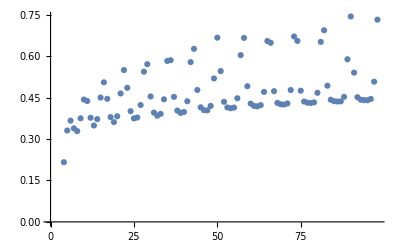

```mathematica
ListPlot[%]
```

### Semigroups that are not nil-2 ones, nil-3 ones, or monoids

```mathematica
(* Remainder after nil-2 and nil-3 removed *)
```

```mathematica
smgrmdr[lbl_] := Module[{smg,nvals,diff},
smg = numdata["smg"<>lbl];
nvals = Range[Length[smg]]-1;
diff = smg - (1 + numval["smg nil3"<>lbl,nvals]);
{nvals,diff,diff/N[smg]}
]
```

```mathematica
(* Remainder after nil-2, nil-3, and monoids removed *)
```

```mathematica
smgmndrmdr[lbl_] := Module[{smg,mnd,lnmin,nvals,diff},
smg = numdata["smg"<>lbl];
mnd = Join[{0,0},Drop[numdata["mnd"<>lbl],1]];
lnmin = Min[Length[smg],Length[mnd]];
smg = Take[smg,lnmin];
mnd = Take[mnd,lnmin];
nvals = Range[lnmin]-1;
diff = smg - (1 + numval["smg nil3"<>lbl,nvals]+ mnd);
{nvals,diff,diff/N[smg]}
]
```

```mathematica
smgrmdr[""]
```

{{0,1,2,3,4,5,6,7,8,9},{0,0,4,22,178,1796,23962,427682,22507624,46305907836},{0.,0.,0.8,0.916667,0.946809,0.937859,0.836837,0.262757,0.00610951,0.000436938}}

```mathematica
smgmndrmdr[""]
```

{{0,1,2,3,4,5,6,7,8},{0,0,2,15,143,1568,21725,396123,20838627},{0.,0.,0.4,0.625,0.760638,0.818799,0.758713,0.243368,0.00565648}}

```mathematica
smgrmdr[" cmt"]
```

{{0,1,2,3,4,5,6,7,8,9,10},{0,0,2,10,52,301,1987,15184,141807,2195602,141655715},{0.,0.,0.666667,0.833333,0.896552,0.926154,0.927205,0.878145,0.639332,0.190164,0.0402553}}

```mathematica
smgmndrmdr[" cmt"]
```

{{0,1,2,3,4,5,6,7},{0,0,0,5,33,223,1566,12547},{0.,0.,0.,0.416667,0.568966,0.686154,0.730751,0.725638}}

```mathematica
smgrmdr[" scnv"]
```

{{0,1,2,3,4,5,6,7,8,9},{0,0,2,10,56,354,2662,24764,358586,17395172},{0.,0.,0.666667,0.833333,0.875,0.874074,0.803744,0.558125,0.162268,0.0278996}}

```mathematica
smgmndrmdr[" scnv"]
```

{{0,1,2,3,4,5,6,7,8},{0,0,0,5,37,270,2153,20863,309629},{0.,0.,0.,0.416667,0.578125,0.666667,0.65006,0.470205,0.140114}}

```mathematica
smgrmdr[" lbl"]
```

{{0,1,2,3,4,5,6,7,8,9},{0,0,7,106,3311,172011,13971867,1798975991,847072308385,16761524547060829},{0.,0.,0.875,0.938053,0.948167,0.936206,0.81893,0.232334,0.00571592,0.00043596}}

```mathematica
smgmndrmdr[" lbl"]
```

{{0,1,2,3,4,5,6,7,8},{0,0,3,73,2687,151401,12719835,1669423911,783930375779},{0.,0.,0.375,0.646018,0.769473,0.824032,0.745545,0.215603,0.00528984}}

```mathematica
smgrmdr[" cmt lbl"]
```

{{0,1,2,3,4,5,6,7},{0,0,5,56,1055,29109,1117901,58707781},{0.,0.,0.833333,0.888889,0.925439,0.94725,0.943319,0.884644}}

```mathematica
smgmndrmdr[" cmt lbl"]
```

{{0,1,2,3,4,5,6,7},{0,0,1,29,679,21679,884561,48694687},{0.,0.,0.166667,0.460317,0.595614,0.705467,0.74642,0.73376}}

### Monoids that are not trivial-action group-semigroup combinations

```mathematica
Range[Length[numdata["mnd flip"]]]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
numdata["mnd flip"] - numval["mnd tvlact flip",%]
```

{0,0,0,2,5,58,428,5539,101082,9269715}

```mathematica
%/N[numdata["mnd flip"]]
```

{0.,0.,0.,0.0740741,0.0320513,0.0422433,0.0241399,0.00644837,0.0000548145,1.74929×10^-7}

### Average Number of Groups

```mathematica
(* Summation done recursively to avoid loss of significance *)
```

```mathematica
sumf[f_,n1_,n2_] := Which[n2>n1,Block[{nm1,nm2},nm1 = Floor[(n1+n2)/2];nm2 = nm1+1; sumf[f,n1,nm1] + sumf[f,nm2,n2]], n2==n1,f[n1],True,0]
```

```mathematica
(* For averaging group counts with weight 1/n and for skipping over missing values *)
```

```mathematica
abgavf[n_] := {1,FiniteAbelianGroupCount[n]}/N[n]
```

```mathematica
grpavf[n_] := Block[{ng},ng = FiniteGroupCount[n];
If[Head[ng] === Integer,{1,ng}/N[n],{0.,0.}]
]
```

```mathematica
avgsum[x_] := x[[2]]/x[[1]]
```

```mathematica
abgavg[nmax_] := avgsum[sumf[abgavf,1,nmax]]
```

```mathematica
grpavg[nmax_] := avgsum[sumf[grpavf,1,nmax]]
```

```mathematica
agagasymp[nmax_] := Block[{z,zprod = 1.},Do[z = Zeta[N[k]]; If[z ==1,Break[]]; zprod *=z,{k,2,nmax}];zprod]
```

```mathematica
agagasymp[1000]
```

2.29486

## Generation of Algebras

### Functions

```mathematica
(* Needs operation table and permutation *)
```

```mathematica
matpermute[mat_,rowperm_,colperm_] := #[[colperm]]& /@ mat[[rowperm]]
```

```mathematica
permauto[mtbl_,perm_] := Module[{n,seq,pminv},
n = Length[mtbl];
seq = Range[n];
pminv = seq /. Thread[perm -> seq];
matpermute[mtbl,pminv,pminv] /. Thread[seq->perm]
]
```

```mathematica
(* Needs permutation list *)
```

```mathematica
ampmlst[mtbl_,pmlist_] := Union @Table[permauto[mtbl,perm],{perm,pmlist}]
```

```mathematica
(* with transpose *)
```

```mathematica
amtppmlst[mtbl_,pmlist_] := Union @@ Table[{#,Transpose[#]}& @ permauto[mtbl,perm],{perm,pmlist}]
```

```mathematica
(* For list of matrices *)
```

```mathematica
ampmmtlst[mtblist_,pmlist_] := Union @ Table[ampmlst[mtbl,pmlist],{mtbl,mtblist}]
```

```mathematica
amtppmmtlst[mtblist_,pmlist_] := Union @ Table[amtppmlst[mtbl,pmlist],{mtbl,mtblist}]
```

```mathematica
(* Select commutative *)
```

```mathematica
IsCommutative[mat_] := mat === Transpose[mat]
```

```mathematica
IsNonCommutative[mat_] := !IsCommutative[mat]
```

```mathematica
(* Self-converse / self-dual in general *)
```

```mathematica
IsSelfConverse[matlist_] := MemberQ[matlist,Transpose[First[matlist]]]
```

```mathematica
SelSelfConverse[matlists_] := Select[matlists,IsSelfConverse]
```

```mathematica
(* Self-converse / self-dual *)
```

```mathematica
IsSelfConvNonCmt[matlist_] := If[IsNonCommutative[First[matlist]],MemberQ[matlist,Transpose[First[matlist]]]]
```

```mathematica
SelSelfConvNonCmt[matlists_] := Select[matlists,IsSelfConvNonCmt]
```

```mathematica
allperms[n_] := Permutations[Range[n]]
```

```mathematica
onefixperms[n_] := Prepend[#,1]& /@ Permutations[Range[2,n]]
```

```mathematica
makecmtmat[n_,matels_] := Module[{meblks,ix,bk,k1,k2},
meblks = Table[ix = n(n+1)/2-k(k+1)/2; Take[matels,{ix+1,ix+k}],{k,n,1,-1}];
Table[k1 = Min[i,j]; k2 = Max[i,j]; meblks[[k1,k2-k1+1]],{i,n},{j,n}]
]
```

```mathematica
(* Adds identity at index 1 *)
```

```mathematica
addident[mtbl_] := Module[{n,id},
n = Length[mtbl];
If[n==0,Return[{{1}}]];
id = Range[2,n+1];
ArrayFlatten[{{{{1}},{id}},{Transpose[{id}],mtbl}}]
]
```

```mathematica
(* Moves the first row and column to all the other positions, exchanges symbols appropriately *)
```

```mathematica
moveident[mtbl_] := Module[{n,id,pmt},
n = Length[mtbl];
If[n == 0,Return[{mtbl}]];
id = Range[n];
Table[pmt = id; pmt[[1]] = k; pmt[[k]] = 1;
permauto[mtbl,pmt],
{k,n}]
]
```

```mathematica
mvidlist[mtbllist_] := Union @@ (moveident /@ mtbllist)
```

```mathematica
mvidmltlist[mtbllists_] := Sort[mvidlist /@ mtbllists]
```

### Groupoids

```mathematica
(* General *)
```

```mathematica
AllGpds["gpd",n_] := If[n>0,Partition[#,n]& /@ Tuples[Range[n],n^2],{{}}]
```

```mathematica
AllGpdSets["gpd",n_] := ampmmtlst[AllGpds["gpd",n],allperms[n]]
```

```mathematica
AllGpdSets["gpd flip",n_] := amtppmmtlst[AllGpds["gpd",n],allperms[n]]
```

```mathematica
AllGpdSets["gpd scnv",n_] := SelSelfConverse[AllGpdSets["gpd",n]]
```

```mathematica
(* Commutative *)
```

```mathematica
AllGpds["gpd cmt",n_] := If[n>0,makecmtmat[n,#]& /@ Tuples[Range[n],n(n+1)/2],{{}}]
```

```mathematica
AllGpdSets["gpd cmt",n_] := ampmmtlst[AllGpds["gpd cmt",n],allperms[n]]
```

```mathematica
(* Identity element is 1 *)
```

```mathematica
AllGpds["gpd id",n_] := If[n>0,If[n>1,addident[Partition[#,n-1]]& /@ Tuples[Range[n],(n-1)^2],{{{1}}}],{}]
```

```mathematica
AllGpdSets["gpd id",n_] := ampmmtlst[AllGpds["gpd id",n],onefixperms[n]]
```

```mathematica
AllGpdSets["gpd id flip",n_] := amtppmmtlst[AllGpds["gpd id",n],onefixperms[n]]
```

```mathematica
AllGpdSets["gpd id scnv",n_] := SelSelfConverse[AllGpdSets["gpd id",n]]
```

```mathematica
(* Commutative *)
```

```mathematica
AllGpds["gpd id cmt",n_] := If[n>0,If[n>1,addident[makecmtmat[n-1,#]]& /@ Tuples[Range[n],n(n-1)/2],{{{1}}}],{}]
```

```mathematica
AllGpdSets["gpd id cmt",n_] := ampmmtlst[AllGpds["gpd id cmt",n],onefixperms[n]]
```

```mathematica
(* Identity element is any *)
```

```mathematica
AllGpds["gpd idx",n_] := mvidlist[AllGpds["gpd id",n]]
```

```mathematica
AllGpdSets["gpd idx",n_] := mvidmltlist[AllGpdSets["gpd id",n]]
```

```mathematica
AllGpdSets["gpd idx flip",n_] :=  mvidmltlist[AllGpdSets["gpd id flip",n]]
```

```mathematica
AllGpdSets["gpd idx scnv",n_] :=  mvidmltlist[AllGpdSets["gpd id scnv",n]]
```

```mathematica
(* Commutative *)
```

```mathematica
AllGpds["gpd idx cmt",n_] := mvidlist[AllGpds["gpd id cmt",n]]
```

```mathematica
AllGpdSets["gpd idx cmt",n_] := mvidmltlist[AllGpdSets["gpd id cmt",n]]
```

### Quasigroups, Loops, and Latin Squares

```mathematica
(* Reduced Latin Squares *)
```

```mathematica
(* Identity element is 1 *)
```

```mathematica
AllGpds["loop",n_] := Module[{perms,lrs,pmrs},
If[n≤0,Return[{}]];
perms = Permutations[Range[n]];
lrs = {{Range[n]}};
Do[
pmrs = Select[perms,First[#]==k&];
lrs = Join @@ Table[If[Min[Min[Abs[#-pm]]& /@ lr]>0,Append[lr,pm],Nothing],{lr,lrs},{pm,pmrs}];,
{k,2,n}];
lrs
]
```

```mathematica
AllGpdSets["loop",n_] := ampmmtlst[AllGpds["loop",n],onefixperms[n]]
```

```mathematica
AllGpdSets["loop flip",n_] := amtppmmtlst[AllGpds["loop",n],onefixperms[n]]
```

```mathematica
AllGpdSets["loop scnv",n_] := SelSelfConverse[AllGpdSets["loop",n]]
```

```mathematica
(* Commutative ones *)
```

```mathematica
AllGpds["loop cmt",n_] := Module[{perms,lrs,pmrs},
If[n≤0,Return[{}]];
perms = Permutations[Range[n]];
lrs = {{Range[n]}};
Do[
pmrs = Select[perms,First[#]==k&];
lrs = Join @@ Table[If[lr[[;;,k]] === pm[[;;k-1]],If[Min[Min[Abs[#-pm]]& /@ lr]>0,Append[lr,pm],Nothing],Nothing],{lr,lrs},{pm,pmrs}];,
{k,2,n}];
lrs
]
```

```mathematica
AllGpdSets["loop cmt",n_] := ampmmtlst[AllGpds["loop cmt",n],onefixperms[n]]
```

```mathematica
(* Identity element is any *)
```

```mathematica
AllGpds["loopx",n_] := mvidlist[AllGpds["loop",n]]
```

```mathematica
AllGpdSets["loopx",n_] := mvidmltlist[AllGpdSets["loop",n]]
```

```mathematica
AllGpdSets["loopx flip",n_] := mvidmltlist[AllGpdSets["loop flip",n]]
```

```mathematica
AllGpdSets["loopx scnv",n_] := mvidmltlist[AllGpdSets["loop scnv",n]]
```

```mathematica
(* Commutative ones *)
```

```mathematica
AllGpds["loopx cmt",n_] := mvidlist[AllGpds["loop cmt",n]]
```

```mathematica
AllGpdSets["loopx cmt",n_] := mvidmltlist[AllGpdSets["loop cmt",n]]
```

```mathematica
(* General Latin Squares *)
```

```mathematica
AllGpds["qsg",n_] := If[n>0,Sort[Flatten[Table[matpermute[mat,rowp,colp],{mat,AllGpds["loop",n]},{rowp,allperms[n]},{colp,onefixperms[n]}],2]],{{}}]
```

```mathematica
AllGpdSets["qsg",n_] := ampmmtlst[AllGpds["qsg",n],allperms[n]]
```

```mathematica
AllGpdSets["qsg flip",n_] := amtppmmtlst[AllGpds["qsg",n],allperms[n]]
```

```mathematica
AllGpdSets["qsg scnv",n_] := SelSelfConverse[AllGpdSets["qsg",n]]
```

```mathematica
(* Commutative ones *)
```

```mathematica
AllGpds["qsg cmt",n_] := If[n>0,Sort[Flatten[Table[mat /. Thread[Range[n]->perm],{mat,AllGpds["loop cmt",n]},{perm,allperms[n]}],1]],{{}}]
```

```mathematica
AllGpdSets["qsg cmt",n_] := ampmmtlst[AllGpds["qsg cmt",n],allperms[n]]
```

```mathematica
(* Latin square to and from three-column form: row index, column index, value *)
```

```mathematica
lstocl[mat_] := Module[{n},
n = Length[mat];
Sort[Flatten[Table[{i,j,mat[[i,j]]},{i,n},{j,n}],1]]
]
```

```mathematica
cltols[cl_] := Normal[SparseArray[#[[{1,2}]]->#[[3]]& /@ cl]]
```

```mathematica
permrule[perm_] := Thread[Range[Length[perm]]->perm]
```

```mathematica
lsclpms[1] = {Range[3]}; lsclpms[2] = {Range[3],{2,1,3}}; lsclpms[3] = Permutations[Range[3]];
```

```mathematica
mkpmcols[clpm_,cl_] := #[[clpm]]& /@ cl
```

```mathematica
lsshrdperm[mat_,n_,cn_:1] := Union @@ Table[cltols[mkpmcols[clp,lstocl[mat]]  /. permrule[perm]],{perm,allperms[n]},{clp,lsclpms[cn]}]
```

```mathematica
lsred[mat_] := SortBy[Transpose[SortBy[Transpose[mat],First]],First]
```

```mathematica
lsindvperm[mat_,n_,cn_:1] := Union @@ Table[lsred[cltols[mkpmcols[clp,lstocl[mat]]] /. permrule[perm]],{perm,allperms[n]},{clp,lsclpms[cn]}]
```

```mathematica
ltsqcmbn[f_,src_] := Union[Table[f[mat],{mat,src}]]
```

```mathematica
AllGpds["ltsq",n_] := AllGpds["qsg",n]
```

```mathematica
(* Equivalent to AllGpdSets["qsg",n] *)
```

```mathematica
(* For permutations shared across row, column, and symbol *)
```

```mathematica
AllGpdSets["ltsq shrdnmpm",n_] := ltsqcmbn[lsshrdperm[#,n]&,AllGpds["qsg",n]]
```

```mathematica
(* Equivalent to sets of flipped quasigroups *)
```

```mathematica
AllGpdSets["ltsq shrdnmpm tp",n_] := ltsqcmbn[lsshrdperm[#,n,2]&,AllGpds["qsg",n]]
```

```mathematica
(* ? *)
```

```mathematica
AllGpdSets["ltsq shrdnmpm rcs",n_] := ltsqcmbn[lsshrdperm[#,n,3]&,AllGpds["qsg",n]]
```

```mathematica
(* For permutations individually for row, column, and value - results given in reduced form *)
```

```mathematica
AllGpdSets["ltsq indvnmpm",n_] :=  ltsqcmbn[lsindvperm[#,n]&,AllGpds["loop",n]]
```

```mathematica
AllGpdSets["ltsq indvnmpm tp",n_] :=  ltsqcmbn[lsindvperm[#,n,2]&,AllGpds["loop",n]]
```

```mathematica
AllGpdSets["ltsq indvnmpm rcs",n_] :=  ltsqcmbn[lsindvperm[#,n,3]&,AllGpds["loop",n]]
```

## Small Semigroups

### Data

```mathematica
(* From Wikipedia *)
```

```mathematica
sgs0 = {{1,"Empty",{}}};
```

```mathematica
sgs1 = {{1,"Trivial",{{1}}}};
```

```mathematica
sgs2 = {{1,"Group Z2",{{1,2},{2,1}}},{2,"Bool And",{{1,1},{1,2}}},{3,"Null",{{1,1},{1,1}}},{4,"Left zero",{{1,1},{2,2}}},{4,"Right zero",{{1,2},{1,2}}}};
```

```mathematica
sgs3 = {{1,"Group Z3",{{1,2,3},{2,3,1},{3,1,2}}},{2,"",{{2,3,2},{3,2,3},{2,3,2}}},{3,"",{{2,3,3},{3,3,3},{3,3,3}}},{4,"{-1,0,1} mult",{{3,2,1},{2,2,2},{1,2,3}}},{5,"",{{3,1,1},{1,2,3},{1,3,3}}},{6,"",{{3,1,1},{1,3,3},{1,3,3}}},{7,"Null",{{3,3,3},{3,3,3},{3,3,3}}},{8,"",{{3,3,3},{3,2,3},{3,3,3}}},{9,"",{{3,2,3},{2,2,2},{3,2,3}}},{10,"",{{3,1,3},{1,2,3},{3,3,3}}},{11,"",{{3,3,3},{2,2,2},{3,3,3}}},{11,"",{{3,2,3},{3,2,3},{3,2,3}}},{12,"",{{3,3,3},{1,2,3},{3,3,3}}},{12,"",{{3,1,3},{3,2,3},{3,3,3}}},{13,"",{{1,2,3},{2,2,3},{3,3,3}}},{14,"",{{1,3,3},{3,2,3},{3,3,3}}},{15,"",{{1,1,1},{2,2,2},{1,1,3}}},{15,"",{{1,2,1},{1,2,1},{1,2,3}}},{16,"",{{1,1,3},{2,2,3},{3,3,3}}},{16,"",{{1,2,3},{1,2,3},{3,3,3}}},{17,"Left zero",{{1,1,1},{2,2,2},{3,3,3}}},{17,"Right zero",{{1,2,3},{1,2,3},{1,2,3}}},{18,"Left flip-flop",{{1,1,1},{2,2,2},{1,2,3}}},{18,"Right flip-flop",{{1,2,1},{1,2,2},{1,2,3}}}};
```

```mathematica
(* From Foster's SWAC results *)
```

```mathematica
swac0 = {{}};
```

```mathematica
swac1 = {{{1}}};
```

```mathematica
swac2 = {{{1,1},{1,1}},{{1,1},{1,2}},{{1,1},{2,2}},{{1,2},{2,1}}};
```

```mathematica
swac3 = {{{1,1,1},{1,1,1},{1,1,1}},{{1,1,1},{1,1,1},{1,1,2}},{{1,1,1},{1,1,1},{1,1,3}},{{1,1,1},{1,1,1},{1,2,3}},{{1,1,1},{1,1,1},{3,3,3}},{{1,1,1},{1,1,2},{1,2,3}},{{1,1,1},{1,2,1},{1,1,3}},{{1,1,1},{1,2,1},{3,3,3}},{{1,1,1},{1,2,2},{1,2,2}},{{1,1,1},{1,2,2},{1,2,3}},{{1,1,1},{1,2,2},{1,3,3}},{{1,1,1},{1,2,3},{1,3,2}},{{1,1,1},{1,2,3},{3,3,3}},{{1,1,1},{2,2,2},{3,3,3}},{{1,1,3},{1,1,3},{3,3,1}},{{1,1,3},{1,2,3},{3,3,1}},{{1,2,2},{2,1,1},{2,1,1}},{{1,2,3},{2,3,1},{3,1,2}}};
```

```mathematica
swac4 = {{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,2}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,1,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,2,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,2,2}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,3,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,2,2,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{4,4,4,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,2},{1,1,2,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,2},{1,1,2,2}},{{1,1,1,1},{1,1,1,1},{1,1,1,2},{1,1,2,3}},{{1,1,1,1},{1,1,1,1},{1,1,1,3},{1,1,3,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,3},{1,2,1,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,1,2,1},{1,1,1,2}},{{1,1,1,1},{1,1,1,1},{1,1,2,1},{1,1,1,4}},{{1,1,1,1},{1,1,1,1},{1,1,2,1},{1,1,2,2}},{{1,1,1,1},{1,1,1,1},{1,1,2,1},{4,4,4,4}},{{1,1,1,1},{1,1,1,1},{1,1,2,2},{1,1,2,2}},{{1,1,1,1},{1,1,1,1},{1,1,3,1},{1,1,1,4}},{{1,1,1,1},{1,1,1,1},{1,1,3,1},{1,2,1,4}},{{1,1,1,1},{1,1,1,1},{1,1,3,1},{4,4,4,4}},{{1,1,1,1},{1,1,1,1},{1,1,3,3},{1,1,3,3}},{{1,1,1,1},{1,1,1,1},{1,1,3,3},{1,1,3,4}},{{1,1,1,1},{1,1,1,1},{1,1,3,3},{1,1,4,4}},{{1,1,1,1},{1,1,1,1},{1,1,3,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,1,3,4},{1,1,4,3}},{{1,1,1,1},{1,1,1,1},{1,1,3,4},{4,4,4,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,1},{4,4,4,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,3},{1,2,3,3}},{{1,1,1,1},{1,1,1,1},{1,2,3,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,3},{1,2,4,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,4},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,4},{1,2,4,3}},{{1,1,1,1},{1,1,1,1},{1,2,3,4},{4,4,4,4}},{{1,1,1,1},{1,1,1,1},{3,3,3,3},{3,3,3,3}},{{1,1,1,1},{1,1,1,1},{3,3,3,3},{3,3,3,4}},{{1,1,1,1},{1,1,1,1},{3,3,3,3},{4,4,4,4}},{{1,1,1,1},{1,1,1,2},{1,1,1,2},{1,2,2,4}},{{1,1,1,1},{1,1,1,2},{1,1,1,2},{1,2,3,4}},{{1,1,1,1},{1,1,1,2},{1,1,1,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,2},{1,1,2,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,2},{1,1,3,1},{1,2,1,4}},{{1,1,1,1},{1,1,1,2},{1,1,3,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,2},{1,2,3,1},{1,1,1,4}},{{1,1,1,1},{1,1,1,2},{1,2,3,2},{1,1,1,4}},{{1,1,1,1},{1,1,1,2},{1,2,3,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{1,1,1,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{1,1,3,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{1,2,1,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{3,3,3,4}},{{1,1,1,1},{1,1,1,3},{3,3,3,3},{4,4,4,4}},{{1,1,1,1},{1,1,2,2},{1,2,3,3},{1,2,3,3}},{{1,1,1,1},{1,1,2,2},{1,2,3,3},{1,2,3,4}},{{1,1,1,1},{1,1,2,2},{1,2,3,3},{1,2,4,4}},{{1,1,1,1},{1,1,2,2},{1,2,3,4},{1,2,4,3}},{{1,1,1,1},{1,2,1,1},{1,1,3,1},{1,1,1,4}},{{1,1,1,1},{1,2,1,1},{1,1,3,1},{4,4,4,4}},{{1,1,1,1},{1,2,1,1},{1,1,3,3},{1,1,3,3}},{{1,1,1,1},{1,2,1,1},{1,1,3,3},{1,1,3,4}},{{1,1,1,1},{1,2,1,1},{1,1,3,3},{1,1,4,4}},{{1,1,1,1},{1,2,1,1},{1,1,3,4},{1,1,4,3}},{{1,1,1,1},{1,2,1,1},{1,1,3,4},{4,4,4,4}},{{1,1,1,1},{1,2,1,1},{3,3,3,3},{3,3,3,4}},{{1,1,1,1},{1,2,1,1},{3,3,3,3},{4,4,4,4}},{{1,1,1,1},{1,2,1,2},{1,1,3,3},{1,2,3,4}},{{1,1,1,1},{1,2,1,2},{3,3,3,3},{1,2,1,2}},{{1,1,1,1},{1,2,1,2},{3,3,3,3},{1,2,1,4}},{{1,1,1,1},{1,2,1,2},{3,3,3,3},{1,2,3,4}},{{1,1,1,1},{1,2,1,2},{3,3,3,3},{1,4,1,4}},{{1,1,1,1},{1,2,1,2},{3,3,3,3},{3,4,3,4}},{{1,1,1,1},{1,2,1,4},{3,3,3,3},{1,2,1,4}},{{1,1,1,1},{1,2,1,4},{3,3,3,3},{1,4,1,2}},{{1,1,1,1},{1,2,1,4},{3,3,3,3},{4,4,4,4}},{{1,1,1,1},{1,2,2,2},{1,2,2,2},{1,2,2,2}},{{1,1,1,1},{1,2,2,2},{1,2,2,2},{1,2,2,3}},{{1,1,1,1},{1,2,2,2},{1,2,2,2},{1,2,2,4}},{{1,1,1,1},{1,2,2,2},{1,2,2,2},{1,2,3,4}},{{1,1,1,1},{1,2,2,2},{1,2,2,2},{1,4,4,4}},{{1,1,1,1},{1,2,2,2},{1,2,2,3},{1,2,3,4}},{{1,1,1,1},{1,2,2,2},{1,2,3,2},{1,2,2,4}},{{1,1,1,1},{1,2,2,2},{1,2,3,2},{1,4,4,4}},{{1,1,1,1},{1,2,2,2},{1,2,3,3},{1,2,3,3}},{{1,1,1,1},{1,2,2,2},{1,2,3,3},{1,2,3,4}},{{1,1,1,1},{1,2,2,2},{1,2,3,3},{1,2,4,4}},{{1,1,1,1},{1,2,2,2},{1,2,3,4},{1,2,4,3}},{{1,1,1,1},{1,2,2,2},{1,2,3,4},{1,4,4,4}},{{1,1,1,1},{1,2,2,2},{1,3,3,3},{1,4,4,4}},{{1,1,1,1},{1,2,2,4},{1,2,2,4},{1,4,4,2}},{{1,1,1,1},{1,2,2,4},{1,2,2,4},{4,4,4,4}},{{1,1,1,1},{1,2,2,4},{1,2,3,4},{1,4,4,2}},{{1,1,1,1},{1,2,2,4},{1,2,3,4},{4,4,4,4}},{{1,1,1,1},{1,2,2,4},{1,3,3,4},{4,4,4,4}},{{1,1,1,1},{1,2,3,3},{1,3,2,2},{1,3,2,2}},{{1,1,1,1},{1,2,3,4},{1,2,3,4},{4,4,4,4}},{{1,1,1,1},{1,2,3,4},{1,3,2,4},{4,4,4,4}},{{1,1,1,1},{1,2,3,4},{1,3,4,2},{1,4,2,3}},{{1,1,1,1},{1,2,3,4},{3,3,3,3},{3,4,1,2}},{{1,1,1,1},{1,2,3,4},{3,3,3,3},{4,4,4,4}},{{1,1,1,1},{2,2,2,2},{3,3,3,3},{4,4,4,4}},{{1,1,1,4},{1,1,1,4},{1,1,1,4},{4,4,4,1}},{{1,1,1,4},{1,1,1,4},{1,1,2,4},{4,4,4,1}},{{1,1,1,4},{1,1,1,4},{1,1,3,4},{4,4,4,1}},{{1,1,1,4},{1,1,1,4},{1,2,3,4},{4,4,4,1}},{{1,1,1,4},{1,1,2,4},{1,2,3,4},{4,4,4,1}},{{1,1,1,4},{1,2,1,4},{1,1,3,4},{4,4,4,1}},{{1,1,1,4},{1,2,2,4},{1,2,2,4},{4,4,4,1}},{{1,1,1,4},{1,2,2,4},{1,2,3,4},{4,4,4,1}},{{1,1,1,4},{1,2,2,4},{1,3,3,4},{4,4,4,1}},{{1,1,1,4},{1,2,3,4},{1,3,2,4},{4,4,4,1}},{{1,1,3,3},{1,1,3,3},{3,3,1,1},{3,3,1,1}},{{1,1,3,3},{1,1,3,3},{3,3,1,1},{3,3,1,2}},{{1,1,3,3},{1,2,3,3},{3,3,1,1},{3,3,1,1}},{{1,1,3,3},{1,2,3,3},{3,3,1,1},{3,4,1,1}},{{1,1,3,3},{1,2,3,4},{3,3,1,1},{3,4,1,1}},{{1,1,3,3},{1,2,3,4},{3,3,1,1},{3,4,1,2}},{{1,1,3,3},{2,2,4,4},{1,1,3,3},{2,2,4,4}},{{1,1,3,3},{2,2,4,4},{3,3,1,1},{4,4,2,2}},{{1,1,3,4},{1,1,3,4},{3,3,4,1},{4,4,1,3}},{{1,1,3,4},{1,2,3,4},{3,3,4,1},{4,4,1,3}},{{1,2,2,2},{2,1,1,1},{2,1,1,1},{2,1,1,1}},{{1,2,2,4},{2,4,4,1},{2,4,4,1},{4,1,1,2}},{{1,2,3,4},{2,1,4,3},{3,4,1,2},{4,3,2,1}},{{1,2,3,4},{2,1,4,3},{3,4,2,1},{4,3,1,2}}};
```

```mathematica
rawmbk3 = "aaa aaa aab --- aaa aaa abc - aba aba abc";
```

```mathematica
rawmbk4 = "aaaa aaaa aaab aabc - aaaa aaaa aaaa aabb - aaaa aaaa aabb aaba --- aaaa aaaa aabb aaab - aaaa aaaa aaba aaab - aaaa aaaa aaab aaba - aaaa aaaa aaaa aaba --- abaa babb abaa abac - abab baba abab babc - abca abca abcb abca - abaa abaa abaa abac --- abaa abaa abcd abcd - abaa abbb abcd abcd - aaaa aaaa abcd abcd --- aaaa aabb aacd aacd - abaa abaa abcc abdd - abaa abbb abcc abdd --- abaa abbb abcd abdc - abab abba abcd abdc - abbb abbb abcd abdc - aaaa aaaa abcd abdc --- aaaa abcd abcd adda - abaa babb abcd abcd - aaaa aabb abcd abdc - abaa babb abcd abdc --- aaaa aaab aaac aaad - aaaa aaab aaaa aacd - abca abca abca abcd --- abca abcb abca abcd - abaa abaa abac abad - abaa abab abac abad --- abaa abab abaa abcd - abaa abaa abaa abcd - abab abab abab abcd - abbb abbb abbc abcd --- aaaa aaab aaac abad - aaaa aaab aaac abbd - abaa babb abaa abcd - abba baab baab abcd --- aaaa aaaa aaaa abbd - aaaa aaaa aaba aaad - abaa abba abca abad - abba abba abca abbd - abbb abbb abcb abbd - aaaa aaba aaca aaad - aaaa aaba aaca abad - aaaa aaba aaca abbd - abaa babb abca abad - aaaa aaba abca aaad - aaaa abba acca aaad - aaaa abca acba aaad - abbb abbb abcc abcd - aaaa aabb aacc aacd - aaaa aaaa aacc abcd";
```

```mathematica
mbk0 = {}; mbk1 = {}; mbk2 = {};
```

```mathematica
mbk3 = {{{1,1,1},{1,1,1},{1,1,2}},{{1,1,1},{1,1,1},{1,2,3}},{{1,1,1},{1,2,1},{3,3,3}}};
```

```mathematica
mbk4 = {{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,2,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,1,2,2}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,2,2,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,1},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,2},{1,1,2,1}},{{1,1,1,1},{1,1,1,1},{1,1,1,2},{1,1,2,2}},{{1,1,1,1},{1,1,1,1},{1,1,1,2},{1,1,2,3}},{{1,1,1,1},{1,1,1,1},{1,1,1,3},{1,2,1,4}},{{1,1,1,1},{1,1,1,1},{1,1,1,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,1,2,1},{1,1,1,2}},{{1,1,1,1},{1,1,1,1},{1,1,2,1},{1,1,1,4}},{{1,1,1,1},{1,1,1,1},{1,1,2,1},{1,1,2,2}},{{1,1,1,1},{1,1,1,1},{1,1,2,1},{4,4,4,4}},{{1,1,1,1},{1,1,1,1},{1,1,3,1},{1,2,1,4}},{{1,1,1,1},{1,1,1,1},{1,1,3,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,1},{4,4,4,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,3},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,3},{1,2,4,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,4},{1,2,3,4}},{{1,1,1,1},{1,1,1,1},{1,2,3,4},{1,2,4,3}},{{1,1,1,1},{1,1,1,1},{1,2,3,4},{4,4,4,4}},{{1,1,1,1},{1,1,1,2},{1,1,1,2},{1,2,3,4}},{{1,1,1,1},{1,1,1,2},{1,1,3,1},{1,2,1,4}},{{1,1,1,1},{1,1,1,2},{1,2,3,1},{1,1,1,4}},{{1,1,1,1},{1,1,1,2},{1,2,3,2},{1,1,1,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{1,1,1,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{1,1,3,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{1,2,1,4}},{{1,1,1,1},{1,1,1,2},{3,3,3,3},{3,3,3,4}},{{1,1,1,1},{1,1,1,3},{3,3,3,3},{4,4,4,4}},{{1,1,1,1},{1,1,2,2},{1,2,3,3},{1,2,4,4}},{{1,1,1,1},{1,1,2,2},{1,2,3,4},{1,2,4,3}},{{1,1,1,1},{1,2,1,1},{1,1,3,1},{4,4,4,4}},{{1,1,1,1},{1,2,1,1},{1,1,3,3},{1,1,4,4}},{{1,1,1,1},{1,2,1,1},{1,1,3,4},{1,1,4,3}},{{1,1,1,1},{1,2,1,1},{1,1,3,4},{4,4,4,4}},{{1,1,1,1},{1,2,1,1},{3,3,3,3},{3,3,3,4}},{{1,1,1,1},{1,2,1,1},{3,3,3,3},{4,4,4,4}},{{1,1,1,1},{1,2,1,2},{3,3,3,3},{1,2,1,4}},{{1,1,1,1},{1,2,1,2},{3,3,3,3},{1,4,1,4}},{{1,1,1,1},{1,2,1,4},{3,3,3,3},{1,2,1,4}},{{1,1,1,1},{1,2,1,4},{3,3,3,3},{1,4,1,2}},{{1,1,1,1},{1,2,1,4},{3,3,3,3},{4,4,4,4}},{{1,1,1,1},{1,2,2,4},{1,3,3,4},{4,4,4,4}},{{1,1,1,1},{1,2,3,4},{1,2,3,4},{4,4,4,4}},{{1,1,1,1},{1,2,3,4},{1,3,2,4},{4,4,4,4}},{{1,1,1,1},{1,2,3,4},{3,3,3,3},{3,4,1,2}},{{1,1,1,4},{1,1,1,4},{1,1,2,4},{4,4,4,1}},{{1,1,1,4},{1,1,1,4},{1,2,3,4},{4,4,4,1}},{{1,1,1,4},{1,2,1,4},{1,1,3,4},{4,4,4,1}},{{1,1,1,4},{1,2,2,4},{1,3,3,4},{4,4,4,1}},{{1,1,1,4},{1,2,3,4},{1,3,2,4},{4,4,4,1}},{{1,1,3,3},{1,1,3,3},{3,3,1,1},{3,3,1,2}},{{1,1,3,3},{1,2,3,3},{3,3,1,1},{3,4,1,1}}};
```

### Analysis

```mathematica
(* Is the table a legitimate groupoid table? *)
```

```mathematica
checktable[mtab_] := Module[{n},
n = Length[mtab];
If[Dimensions[mtab] =!= {n,n},Return[False]];
If[Length[Complement[Flatten[mtab],Range[n]]]>0,Return[False]];
True
]
```

```mathematica
(* Are all the result contents zero? *)
```

```mathematica
testzero[lst_] := Length[Complement[Flatten[lst],{0}]]==0
```

```mathematica
(* Inverse of a permutation *)
```

```mathematica
invperm[p_] := Module[{n,ip},
n= Length[p];
ip = ConstantArray[0,n];
Do[ip[[p[[k]]]] = k,{k,n}];
ip
]
```

```mathematica
(* Relabel an operation table - rlbl has contents destination value for each index *)
```

```mathematica
relabel[rlbl_,mtab_] := Module[{linv},
linv = invperm[rlbl];
Map[rlbl[[#]]&,mtab[[linv,linv]],{2}]
]
```

```mathematica
(* All distinct relabelings, sorted *)
```

```mathematica
rlball[mtab_] := Module[{n},
n = Length[mtab];
Union[Table[relabel[p,mtab],{p,Permutations[Range[n]]}]]
]
```

```mathematica
rlbflpall[mtab_] := Union[rlball[mtab],rlball[Transpose[mtab]]]
```

```mathematica
(* Canonical relabeling *)
```

```mathematica
rlbcan[mtab_] := First[rlball[mtab]]
```

```mathematica
rlbflpcan[mtab_] := First[rlbflpall[mtab]]
```

```mathematica
(* Commutator values *)
```

```mathematica
commutvals[mtab_] := mtab - Transpose[mtab] // Expand
```

```mathematica
commut[mtab_] := testzero[commutvals[mtab]]
```

```mathematica
(* Associator values *)
```

```mathematica
assocvals[mtab_] := Module[{n},
n = Length[mtab];
Table[mtab[[mtab[[i1,i2]],i3]] - mtab[[i1,mtab[[i2,i3]]]],{i1,n},{i2,n},{i3,n}]
]
```

```mathematica
assoc[mtab_] := testzero[assocvals[mtab]]
```

```mathematica
(* Self-adjoint values *)
```

```mathematica
selfadjvals[mtab_] := rlbcan[mtab] - rlbcan[Transpose[mtab]] // Expand
```

```mathematica
selfadj[mtab_] := testzero[selfadjvals[mtab]]
```

```mathematica
(* Left and right identities *)
```

```mathematica
leftident[mtab_] := Module[{n,id},
n = Length[mtab];
id = Range[n];
Select[id,mtab[[#]]===id&]
]
```

```mathematica
rightident[mtab_] := leftident[Transpose[mtab]]
```

```mathematica
ident[mtab_] := Intersection[leftident[mtab],rightident[mtab]]
```

```mathematica
(* Left and right zeros *)
```

```mathematica
leftzero[mtab_] := Module[{n,id},
n = Length[mtab];
id = Range[n];
Select[id,mtab[[#]]===ConstantArray[#,n]&]
]
```

```mathematica
rightzero[mtab_] := leftzero[Transpose[mtab]]
```

```mathematica
zero[mtab_] := Intersection[leftzero[mtab],rightzero[mtab]]
```

```mathematica
(* Idempotents: a*a = a *)
```

```mathematica
idempotents[mtab_] := Module[{n,id},
n = Length[mtab];
id = Range[n];
Select[id,mtab[[#,#]] == #&]
]
```

```mathematica
(* Mult-table powers *)
```

```mathematica
mtpowers[mtab_] := Module[{n,id,next},
n = Length[mtab];
id = Range[n];
next[x_] := Union @@ mtab[[x]];
FixedPointList[next,id] // Most
]
```

```mathematica
(* Element pseudoinverses *)
```

```mathematica
pseudoinverses[mtab_] := Module[{n},
n = Length[mtab];
Table[Select[Range[n],mtab[[i,mtab[[#,i]]]]==i&],{i,n}]
]
```

```mathematica
inverses[mtab_] := Module[{n,psi,ivss,pnvs,j},
n = Length[mtab];
psi = pseudoinverses[mtab];
ivss = Table[pnvs = psi[[i]];If[Length[pnvs]==1,First[pnvs],Null],{i,n}];
Table[j = ivss[[i]];If[j=!=Null,If[ivss[[j]]===i,j,Null],Null],{i,n}]
]
```

```mathematica
setprod[mtab_,xl1_,xl2_] := Union @@ (#[[xl2]]& /@ mtab[[xl1]])
```

```mathematica
(* Left, right, both-side ideals *)
```

```mathematica
ideals[mtab_] := Module[{n,id,idss,next,ss,li,ri,ti},
n = Length[mtab];
id = Range[n];
idss = Subsets[id,{1,n-1}];
ss = Select[idss,SubsetQ[#,setprod[mtab,#,#]]&];
li = Select[idss,SubsetQ[#,setprod[mtab,id,#]]&];
ri = Select[idss,SubsetQ[#,setprod[mtab,#,id]]&];
ti = Intersection[li,ri];
{ss,li,ri,ti}
]
```

```mathematica
elpwrs[mtab_] := Module[{n,pwrseq,pwrnxt},
n = Length[mtab];
Table[
pwrseq = {k};
While[True,
pwrnxt = mtab[[Last[pwrseq],k]];
AppendTo[pwrseq,pwrnxt];
If[MemberQ[Most[pwrseq],pwrnxt],Break[]];
];
pwrseq,
{k,n}]
]
```

```mathematica
qstv[mtab_] := Module[{n},
n = Length[mtab];
And @@ Flatten[Table[MemberQ[{i,j},mtab[[i,j]]],{i,n},{j,n}]]
]
```

```mathematica
sscollect[sss_] := Module[{nsss},
nsss = Transpose[{Range[Length[sss]],sss}];
{First /@ #,Last[First[#]]}& /@ GatherBy[nsss,Last]
]
```

```mathematica
greenrlt[mtab_] := Module[{n,mttr,lfi,rgi,bti,isi,sgssrc,sgs,lft,rgt,btt,sdt,ist,t,xtt},
n = Length[mtab];
(* Find identity-adjoined ideals *)
mttr = Transpose[mtab];
lfi = MapIndexed[Union[#1,#2]&,mttr];
rgi = MapIndexed[Union[#1,#2]&,mtab];
bti = Map[Union[Union @@ mttr[[#]],#]&,rgi];
isi = MapThread[Intersection,{lfi,rgi},1];
(* Find subgroups *)
sgssrc = Table[{k,isi[[k]],isi[[k]]===isi[[mtab[[k,k]]]]},{k,n}];
sgssrc = Most /@ Select[sgssrc,Last];
sgs = (First /@ #)& /@ GatherBy[sgssrc,Last];
(* Tests of Green's relations *)
lft = Outer[SameQ,lfi,lfi,1];
rgt = Outer[SameQ,rgi,rgi,1];
btt = Outer[SameQ,bti,bti,1];
ist = Outer[SameQ,isi,isi,1];
sdt = MapThread[And,{lft,rgt},2];
xtt = Inner[And,lft,rgt,Or];
{sscollect /@ {lfi,rgi,bti,isi},sgs,{ist===sdt,btt===xtt}}
]
```

### Generation

```mathematica
(* Generation of semigroups *)
```

```mathematica
(* Canonicalize the resulting semigroup; make it optional in case one wants a raw result. *)
```

```mathematica
mkcanon[mtab_,canon_:True] := If[canon,rlbflpcan[mtab],mtab]
```

```mathematica
(* Direct product *)
```

```mathematica
mtprod[mtab1_,mtab2_, canon_:True] := Module[{n1,n2,i1,i2,j1,j2},
n1 = Length[mtab1];n2=Length[mtab2];
mkcanon[Normal[SparseArray[Flatten[Table[{n2*(i1-1)+i2,n2*(j1-1)+j2}->(n2*(mtab1[[i1,j1]]-1)+mtab2[[i2,j2]]),{i1,n1},{i2,n2},{j1,n1},{j2,n2}]],(n1*n2)*{1,1}]],canon]
]
```

```mathematica
mtseqprd[mtbseq_,canon_:True] := Fold[mtprod[#,#,canon]&,{{1}},mtbseq]
```

```mathematica
mtlstprod[mtblst1_,mtblst2_,canon_:True] := Union[Flatten[Table[rlbflpcan /@ {mtprod[m1,m2,canon],mtprod[m1,Transpose[m2],canon]},{m1,mtblst1},{m2,mtblst2}],2]]
```

```mathematica
mtlstseqprod[mtblstseq_,canon_:True] := Fold[mtlstprod[#1,,#2,canon]&,{{{1}}},mtblstseq]
```

```mathematica
(* Adjoined identity and zero *)
```

```mathematica
adjzero[mtab_,canon_:True] := Module[{n},
n = Length[mtab];
mkcanon[Transpose[Append[Transpose[Append[mtab,ConstantArray[n+1,n]]],ConstantArray[n+1,n+1]]],canon]
]
```

```mathematica
adjident[mtab_,canon_:True] := Module[{n},
n = Length[mtab];
mkcanon[Transpose[Append[Transpose[Append[mtab,Range[n]]],Range[n+1]]],canon]
]
```

```mathematica
adjidzr[mtab_,canon_:True] := adjzero[adjident[mtab,canon],canon]
```

```mathematica
(* Inflation: for each element a, add some additional elements that behave like a in the operation: x(a)*y(b) = a*b *)
```

```mathematica
inflate[mtab_,amts_,canon_] := Module[{newixs,n},
newixs = Most[Prepend[Accumulate[amts],0]+1];
n = Length[mtab];
mkcanon[ArrayFlatten[Table[ConstantArray[newixs[[mtab[[i,j]]]],{amts[[i]],amts[[j]]}],{i,n},{j,n}]],canon]
]
```

```mathematica
(* Do all inflations by size 1 *)
```

```mathematica
multinflate[mtab_,canon_:True] := Module[{amts},
amts = IdentityMatrix[Length[mtab]]+1;
Union[inflate[mtab,#,canon]& /@ amts]
]
```

```mathematica
(* Constant rows - requires that rows be idempotent - Row function r(i) = r(r(i)) for index i *)
```

```mathematica
(* https://oeis.org/A000248 -- Expansion of e.g.f.exp(x*exp(x)). -- Number of forests with n nodes and height at most 1. -- Equivalently,number of idempotent mappings f from a set of n elements into itself *)
```

```mathematica
(* https://oeis.org/A000041 - number of partitions of n (the partition numbers). *)
```

```mathematica
immptest[f_] := f[[f]]===f
```

```mathematica
immps[n_] := Select[Tuples[Range[n],n],immptest]
```

```mathematica
immpxp[f_] := Module[{n},
n = Length[f];
Table[p[[f[[invperm[p]]]]],{p,Permutations[Range[n]]}]
]
```

```mathematica
immpcn[f_] := First[Union[immpxp[f]]]
```

```mathematica
immprd[n_] := Union[immpcn /@ immps[n]]
```

```mathematica
prtxpnd[prt_] := Module[{n,newixs},
newixs = Most[Accumulate[Prepend[prt,0]]]+1;
n = Length[prt];
Flatten[Table[ConstantArray[newixs[[i]],prt[[i]]],{i,n}]]
]
```

```mathematica
prtxpds[n_] := Union[prtxpnd /@ IntegerPartitions[n]]
```

```mathematica
prtxpdtest[n_] := prtxpds[n] == immprd[n]
```

```mathematica
(* Constant-row semigroups *)
```

```mathematica
cnstrows[n_] := Table[ConstantArray[x,n],{x,#}]& /@ prtxpds[n]
```

```mathematica
(* Nil-3 semigroups *)
```

```mathematica
makenil3[prod_,nscnd_,zero_,canon_] := Module[{n},
n = Length[prod];
mkcanon[ArrayFlatten[{{prod,ConstantArray[zero,{n,nscnd}]},{ConstantArray[zero,{nscnd,n}],ConstantArray[zero,{nscnd,nscnd}]}}],canon]
]
```

```mathematica
(* Semilattice from intersections or unions of sets *)
```

```mathematica
cmtfilloutstep[xlst_,op_] := Module[{newxlst},
newxlst = xlst;
Do[newxlst = Union[newxlst,op[#,x]& /@ newxlst],
{x,xlst}];
newxlst]
```

```mathematica
cmtfillout[xlst_,op_] := FixedPoint[cmtfilloutstep[#,op]&,xlst]
```

```mathematica
smltop[sets_,op_] := Module[{fillsets,n,ixf,tbl},
fillsets = cmtfillout[Union /@ sets,op];
n = Length[fillsets];
Do[ixf[fillsets[[k]]] = k,{k,n}];
tbl = Table[ixf[op[s1,s2]],{s1,fillsets},{s2,fillsets}];
{fillsets,tbl}
]
```

```mathematica
smltitsc[sets_] := smltop[sets,Intersection]
```

```mathematica
smltunion[sets_] := smltop[sets,Union]
```

```mathematica
(* Full lattices from sets *)
```

```mathematica
latfilloutstep[sets_] := Module[{newsets},
newsets = sets;
Do[newsets = Union[newsets,Intersection[#,x]& /@ newsets];
newsets = Union[newsets,Union[#,x]& /@ newsets],
{x,sets}];
newsets]
```

```mathematica
latfillout[sets_] := FixedPoint[latfilloutstep,Union /@ sets]
```

```mathematica
latsets[sets_] := Module[{fillsets,n,ixf,tblitsc,tblunion},
fillsets = latfillout[sets];
n = Length[fillsets];
Do[ixf[fillsets[[k]]] = k,{k,n}];
tblitsc = Table[ixf[Intersection[s1,s2]],{s1,fillsets},{s2,fillsets}];
tblunion = Table[ixf[Union[s1,s2]],{s1,fillsets},{s2,fillsets}];
{fillsets,tblitsc,tblunion}
]
```

```mathematica
(* Mario-book table reduction *)
```

```mathematica
mbkred[mbkstr_] := Sort[rlbflpcan[(Characters /@ StringSplit[#," "]) /. {"a"->1,"b"->2,"c"->3,"d"->4}]& /@  StringSplit[mbkstr," - "|" --- "]]
```

### Tests

```mathematica
assoctest[tbs_] := And @@ (assoc /@ tbs)
```

```mathematica
sgsassoctest[xlst_] := assoctest[#[[3]]& /@ xlst]
```

```mathematica
sgsassoctest[sgs1]
```

True

```mathematica
sgsassoctest[sgs2]
```

True

```mathematica
sgsassoctest[sgs3]
```

True

```mathematica
assoctest[swac1]
```

True

```mathematica
assoctest[swac2]
```

True

```mathematica
assoctest[swac3]
```

True

```mathematica
assoctest[swac4]
```

True

```mathematica
(* Are the SWAC results in canonical form? *)
```

```mathematica
rfctest[xlst_] := testzero[xlst - (rlbflpcan /@ xlst)]
```

```mathematica
rfctest[swac2]
```

True

```mathematica
rfctest[swac3]
```

True

```mathematica
rfctest[swac4]
```

True

```mathematica
Complement[mbk3,swac3]
```

{}

```mathematica
Complement[mbk4,swac4]
```

{}

### Composition

```mathematica
adjlstident[xlst_] := Union[adjident /@ xlst]
```

```mathematica
adjlstzero[xlst_] := Union[adjzero /@ xlst]
```

```mathematica
adjlstidzr[xlst_] := Union[adjidzr /@ xlst]
```

```mathematica
multinfllist[xlst_] := Union @@ (multinflate/@ xlst)
```

```mathematica
cycgrp[n_] := mkcanon[Outer[Mod[#1+#2,n]+1&,Range[0,n-1],Range[0,n-1]]]
```

```mathematica
cmbnlist[xlst_] := Union[adjlstident[xlst],adjlstzero[xlst],multinfllist[xlst],cnstrows[Length[First[xlst]]+1],{cycgrp[Length[First[xlst]]+1]}]
```

```mathematica
adjlstident[swac0] == swac1
```

True

```mathematica
adjlstzero[swac0] == swac1
```

True

```mathematica
MatrixForm /@ Join[adjlstident[swac1],adjlstzero[swac1],adjlstidzr[swac0]]
```

{(1 | 1
1 | 2),(1 | 1
1 | 2),(1 | 1
1 | 2)}

```mathematica
MatrixForm /@ multinfllist[swac1]
```

{(1 | 1
1 | 1)}

```mathematica
MatrixForm /@ Complement[swac2,cmbnlist[swac1]]
```

{}

```mathematica
(* Try to find missing patterns *)
```

```mathematica
MatrixForm /@ Complement[swac3,cmbnlist[swac2],mbk3]
```

{(1 | 1 | 1
1 | 2 | 1
1 | 1 | 3)}

```mathematica
MatrixForm /@ Complement[swac4,mtlstprod[swac2,swac2],cmbnlist[swac3],mbk4]
```

{(1 | 1 | 1 | 1
1 | 2 | 1 | 1
1 | 1 | 3 | 1
1 | 1 | 1 | 4),(1 | 1 | 1 | 1
1 | 2 | 1 | 1
1 | 1 | 3 | 3
1 | 1 | 3 | 4)}

```mathematica
MatrixForm /@ Select[swac3,Diagonal[#]===Range[3] && # === Transpose[#]&]
```

{(1 | 1 | 1
1 | 2 | 1
1 | 1 | 3),(1 | 1 | 1
1 | 2 | 2
1 | 2 | 3)}

```mathematica
MatrixForm /@ Select[swac4,Diagonal[#]===Range[4] && # === Transpose[#]&]
```

{(1 | 1 | 1 | 1
1 | 2 | 1 | 1
1 | 1 | 3 | 1
1 | 1 | 1 | 4),(1 | 1 | 1 | 1
1 | 2 | 1 | 1
1 | 1 | 3 | 3
1 | 1 | 3 | 4),(1 | 1 | 1 | 1
1 | 2 | 1 | 2
1 | 1 | 3 | 3
1 | 2 | 3 | 4),(1 | 1 | 1 | 1
1 | 2 | 2 | 2
1 | 2 | 3 | 2
1 | 2 | 2 | 4),(1 | 1 | 1 | 1
1 | 2 | 2 | 2
1 | 2 | 3 | 3
1 | 2 | 3 | 4)}

### Display

```mathematica
showtab[mtab_] := StringRiffle[Map[StringJoin @@ (ToString /@ #)&,mtab],"."]
```

```mathematica
showcommut[mtab_] := If[commut[mtab],"C",""]
```

```mathematica
showqt[mtab_] := If[qstv[mtab],"Q",""]
```

```mathematica
showidzr[lf_,rg_] := Module[{tot,lfx,rgx,makestr},
tot = Intersection[lf,rg];
lfx = Complement[lf,tot];
rgx = Complement[rg,tot];
makestr[pfx_,lst_] := StringJoin @@ If[Length[lst]>0,Flatten[{pfx,ToString /@ lst}],Nothing];
StringRiffle[{makestr["L",lfx],makestr["R",rgx],makestr["",tot]},","]
]
```

```mathematica
showid[mtab_] := showidzr[leftident[mtab],rightident[mtab]];
```

```mathematica
showzr[mtab_] := showidzr[leftzero[mtab],rightzero[mtab]];
```

```mathematica
showips[mtab_] := StringJoin @@ (ToString /@ idempotents[mtab])
```

```mathematica
lsttostr[xlst_] := StringJoin @@ (ToString /@ xlst)
```

```mathematica
mlsttomstr[xmlst_] := StringRiffle[lsttostr /@ xmlst,","]
```

```mathematica
showmtp[mtab_] := mlsttomstr[mtpowers[mtab]]
```

```mathematica
showinv[mtab_] := mlsttomstr[pseudoinverses[mtab]]
```

```mathematica
showideals[mtab_] :=ToString[StringForm["S`` L`` R`` T``",#1,#2,#3,#4]]& @@ (mlsttomstr /@ ideals[mtab])
```

```mathematica
showfeatures[x_] := Module[{num,name,mtab},
{num,name,mtab} = x;
{num,name,showcommut[mtab],showqt[mtab],showid[mtab],showzr[mtab],showips[mtab],showmtp[mtab],showinv[mtab]}
]
```

```mathematica
showidealfeatures[x_] := Module[{num,name,mtab},
{num,name,mtab} = x;
{num,name,showideals[mtab]}
]
```

```mathematica
hdr = {"Num","Name","Cmt","Qtv","Ids","Zrs","Ips","Pwrs","Inv"};
```

```mathematica
maketab[xlst_] := TableForm[showfeatures /@ xlst,TableDepth->2,TableHeadings->{Automatic,hdr}]
```

```mathematica
idealhdr = {"Num","Name","Ideals"};
```

```mathematica
makeidealtab[xlst_] := TableForm[showidealfeatures /@ xlst,TableDepth->2,TableHeadings->{Automatic,idealhdr}]
```

```mathematica
mtabdisp[sgs_] := Module[{sg},
Table[sg = sgs[[k]]; {k,sg[[1]],sg[[2]],MatrixForm[sg[[3]]]},{k,Length[sgs]}]
]
```

```mathematica
greendisp[mtab_] := Module[{sbsts,sgs,tabs},
{sbsts,sgs,tabs} = greenrlt[mtab];
{If[mtab === Transpose[mtab],TableForm[{{First[sbsts]}},TableHeadings->{{"J"},None},TableDepth->4],TableForm[Transpose[{sbsts}],TableHeadings->{{"L","R","B","H"},None},TableDepth->4]],sgs,tabs}
]
```

```mathematica
mtgrndisp[sgs_] := Module[{sg},
Table[sg = sgs[[k]]; {k,sg[[1]],sg[[2]],greendisp[sg[[3]]]},{k,Length[sgs]}]
]
```

```mathematica
maketab[sgs1]
```

| Num | Name | Cmt | Qtv | Ids | Zrs | Ips | Pwrs | Inv
1 | 1 | Trivial | C | Q | 1 | 1 | 1 | 1 | 1

```mathematica
makeidealtab[sgs1]
```

| Num | Name | Ideals
1 | 1 | Trivial | S L R T

```mathematica
mtabdisp[sgs1]
```

{{1,1,Trivial,(1)}}

```mathematica
mtgrndisp[sgs1]
```

{{1,1,Trivial,{J | {1} | {1},{{1}},{True,True}}}}

```mathematica
maketab[sgs2]
```

| Num | Name | Cmt | Qtv | Ids | Zrs | Ips | Pwrs | Inv
1 | 1 | Group Z2 | C |  | 1 |  | 1 | 12 | 1,2
2 | 2 | Bool And | C | Q | 2 | 1 | 12 | 12 | 12,2
3 | 3 | Null | C |  |  | 1 | 1 | 12,1 | 12,
4 | 4 | Left zero |  | Q | R12 | L12 | 12 | 12 | 12,12
5 | 4 | Right zero |  | Q | L12 | R12 | 12 | 12 | 12,12

```mathematica
makeidealtab[sgs2]
```

| Num | Name | Ideals
1 | 1 | Group Z2 | S1 L R T
2 | 2 | Bool And | S1,2 L1 R1 T1
3 | 3 | Null | S1 L1 R1 T1
4 | 4 | Left zero | S1,2 L R1,2 T
5 | 4 | Right zero | S1,2 L1,2 R T

```mathematica
mtabdisp[sgs2]
```

{{1,1,Group Z2,(1 | 2
2 | 1)},{2,2,Bool And,(1 | 1
1 | 2)},{3,3,Null,(1 | 1
1 | 1)},{4,4,Left zero,(1 | 1
2 | 2)},{5,4,Right zero,(1 | 2
1 | 2)}}

```mathematica
mtgrndisp[sgs2]
```

{{1,1,Group Z2,{J | {1,2} | {1,2},{{1,2}},{True,True}}},{2,2,Bool And,{J | {1} | {1}
{2} | {1,2},{{1},{2}},{True,True}}},{3,3,Null,{J | {1} | {1}
{2} | {1,2},{{1}},{True,True}}},{4,4,Left zero,{L | {1,2} | {1,2}
R | {1} | {1}
{2} | {2}
B | {1,2} | {1,2}
H | {1} | {1}
{2} | {2},{{1},{2}},{True,True}}},{5,4,Right zero,{L | {1} | {1}
{2} | {2}
R | {1,2} | {1,2}
B | {1,2} | {1,2}
H | {1} | {1}
{2} | {2},{{1},{2}},{True,True}}}}

```mathematica
maketab[sgs3]
```

| Num | Name | Cmt | Qtv | Ids | Zrs | Ips | Pwrs | Inv
1 | 1 | Group Z3 | C |  | 1 |  | 1 | 123 | 1,3,2
2 | 2 |  | C |  |  |  | 2 | 123,23 | ,2,13
3 | 3 |  | C |  |  | 3 | 3 | 123,23,3 | ,,123
4 | 4 | {-1,0,1} mult | C |  | 3 | 2 | 23 | 123 | 1,123,3
5 | 5 |  | C |  | 2 |  | 23 | 123 | 1,2,23
6 | 6 |  | C |  |  |  | 3 | 123,13 | 1,,23
7 | 7 | Null | C |  |  | 3 | 3 | 123,3 | ,,123
8 | 8 |  | C |  |  | 3 | 23 | 123,23 | ,2,123
9 | 9 |  | C |  |  | 2 | 23 | 123,23 | ,123,13
10 | 10 |  | C |  | 2 | 3 | 23 | 123 | ,2,123
11 | 11 |  |  |  |  | L23 | 23 | 123,23 | ,123,123
12 | 11 |  |  |  |  | R23 | 23 | 123,23 | ,123,123
13 | 12 |  |  |  | L2 | 3 | 23 | 123 | ,2,123
14 | 12 |  |  |  | R2 | 3 | 23 | 123 | ,2,123
15 | 13 |  | C | Q | 1 | 3 | 123 | 123 | 1,12,123
16 | 14 |  | C |  |  | 3 | 123 | 123 | 1,2,123
17 | 15 |  |  |  | R3 | L12 | 123 | 123 | 123,123,3
18 | 15 |  |  |  | L3 | R12 | 123 | 123 | 123,123,3
19 | 16 |  |  | Q | R12 | 3 | 123 | 123 | 12,12,123
20 | 16 |  |  | Q | L12 | 3 | 123 | 123 | 12,12,123
21 | 17 | Left zero |  | Q | R123 | L123 | 123 | 123 | 123,123,123
22 | 17 | Right zero |  | Q | L123 | R123 | 123 | 123 | 123,123,123
23 | 18 | Left flip-flop |  | Q | 3 | L12 | 123 | 123 | 123,123,3
24 | 18 | Right flip-flop |  | Q | 3 | R12 | 123 | 123 | 123,123,3

```mathematica
makeidealtab[sgs3]
```

| Num | Name | Ideals
1 | 1 | Group Z3 | S1 L R T
2 | 2 |  | S2,23 L23 R23 T23
3 | 3 |  | S3,23 L3,23 R3,23 T3,23
4 | 4 | {-1,0,1} mult | S2,3,13,23 L2 R2 T2
5 | 5 |  | S2,3,13,23 L13 R13 T13
6 | 6 |  | S3,13,23 L13 R13 T13
7 | 7 | Null | S3,13,23 L3,13,23 R3,13,23 T3,13,23
8 | 8 |  | S2,3,13,23 L3,13,23 R3,13,23 T3,13,23
9 | 9 |  | S2,3,13,23 L2,23 R2,23 T2,23
10 | 10 |  | S2,3,13,23 L3,13 R3,13 T3,13
11 | 11 |  | S2,3,13,23 L23 R2,3,13,23 T23
12 | 11 |  | S2,3,13,23 L2,3,13,23 R23 T23
13 | 12 |  | S2,3,13,23 L3,13,23 R3,13 T3,13
14 | 12 |  | S2,3,13,23 L3,13 R3,13,23 T3,13
15 | 13 |  | S1,2,3,12,13,23 L3,23 R3,23 T3,23
16 | 14 |  | S1,2,3,13,23 L3,13,23 R3,13,23 T3,13,23
17 | 15 |  | S1,2,3,12,13 L12 R1,2,12,13 T12
18 | 15 |  | S1,2,3,12,13 L1,2,12,13 R12 T12
19 | 16 |  | S1,2,3,12,13,23 L3 R3,13,23 T3
20 | 16 |  | S1,2,3,12,13,23 L3,13,23 R3 T3
21 | 17 | Left zero | S1,2,3,12,13,23 L R1,2,3,12,13,23 T
22 | 17 | Right zero | S1,2,3,12,13,23 L1,2,3,12,13,23 R T
23 | 18 | Left flip-flop | S1,2,3,12,13,23 L12 R1,2,12 T12
24 | 18 | Right flip-flop | S1,2,3,12,13,23 L1,2,12 R12 T12

```mathematica
mtabdisp[sgs3]
```

{{1,1,Group Z3,(1 | 2 | 3
2 | 3 | 1
3 | 1 | 2)},{2,2,,(2 | 3 | 2
3 | 2 | 3
2 | 3 | 2)},{3,3,,(2 | 3 | 3
3 | 3 | 3
3 | 3 | 3)},{4,4,{-1,0,1} mult,(3 | 2 | 1
2 | 2 | 2
1 | 2 | 3)},{5,5,,(3 | 1 | 1
1 | 2 | 3
1 | 3 | 3)},{6,6,,(3 | 1 | 1
1 | 3 | 3
1 | 3 | 3)},{7,7,Null,(3 | 3 | 3
3 | 3 | 3
3 | 3 | 3)},{8,8,,(3 | 3 | 3
3 | 2 | 3
3 | 3 | 3)},{9,9,,(3 | 2 | 3
2 | 2 | 2
3 | 2 | 3)},{10,10,,(3 | 1 | 3
1 | 2 | 3
3 | 3 | 3)},{11,11,,(3 | 3 | 3
2 | 2 | 2
3 | 3 | 3)},{12,11,,(3 | 2 | 3
3 | 2 | 3
3 | 2 | 3)},{13,12,,(3 | 3 | 3
1 | 2 | 3
3 | 3 | 3)},{14,12,,(3 | 1 | 3
3 | 2 | 3
3 | 3 | 3)},{15,13,,(1 | 2 | 3
2 | 2 | 3
3 | 3 | 3)},{16,14,,(1 | 3 | 3
3 | 2 | 3
3 | 3 | 3)},{17,15,,(1 | 1 | 1
2 | 2 | 2
1 | 1 | 3)},{18,15,,(1 | 2 | 1
1 | 2 | 1
1 | 2 | 3)},{19,16,,(1 | 1 | 3
2 | 2 | 3
3 | 3 | 3)},{20,16,,(1 | 2 | 3
1 | 2 | 3
3 | 3 | 3)},{21,17,Left zero,(1 | 1 | 1
2 | 2 | 2
3 | 3 | 3)},{22,17,Right zero,(1 | 2 | 3
1 | 2 | 3
1 | 2 | 3)},{23,18,Left flip-flop,(1 | 1 | 1
2 | 2 | 2
1 | 2 | 3)},{24,18,Right flip-flop,(1 | 2 | 1
1 | 2 | 2
1 | 2 | 3)}}

```mathematica
mtgrndisp[sgs3]
```

{{1,1,Group Z3,{J | {1,2,3} | {1,2,3},{{1,2,3}},{True,True}}},{2,2,,{J | {1} | {1,2,3}
{2,3} | {2,3},{{2,3}},{True,True}}},{3,3,,{J | {1} | {1,2,3}
{2} | {2,3}
{3} | {3},{{3}},{True,True}}},{4,4,{-1,0,1} mult,{J | {1,3} | {1,2,3}
{2} | {2},{{1,3},{2}},{True,True}}},{5,5,,{J | {1,3} | {1,3}
{2} | {1,2,3},{{1,3},{2}},{True,True}}},{6,6,,{J | {1,3} | {1,3}
{2} | {1,2,3},{{1,3}},{True,True}}},{7,7,Null,{J | {1} | {1,3}
{2} | {2,3}
{3} | {3},{{3}},{True,True}}},{8,8,,{J | {1} | {1,3}
{2} | {2,3}
{3} | {3},{{2},{3}},{True,True}}},{9,9,,{J | {1} | {1,2,3}
{2} | {2}
{3} | {2,3},{{2},{3}},{True,True}}},{10,10,,{J | {1} | {1,3}
{2} | {1,2,3}
{3} | {3},{{2},{3}},{True,True}}},{11,11,,{L | {1} | {1,2,3}
{2,3} | {2,3}
R | {1} | {1,3}
{2} | {2}
{3} | {3}
B | {1} | {1,2,3}
{2,3} | {2,3}
H | {1} | {1,3}
{2} | {2}
{3} | {3},{{2},{3}},{True,True}}},{12,11,,{L | {1} | {1,3}
{2} | {2}
{3} | {3}
R | {1} | {1,2,3}
{2,3} | {2,3}
B | {1} | {1,2,3}
{2,3} | {2,3}
H | {1} | {1,3}
{2} | {2}
{3} | {3},{{2},{3}},{True,True}}},{13,12,,{L | {1} | {1,3}
{2} | {2,3}
{3} | {3}
R | {1} | {1,3}
{2} | {1,2,3}
{3} | {3}
B | {1} | {1,3}
{2} | {1,2,3}
{3} | {3}
H | {1} | {1,3}
{2} | {2,3}
{3} | {3},{{2},{3}},{True,True}}},{14,12,,{L | {1} | {1,3}
{2} | {1,2,3}
{3} | {3}
R | {1} | {1,3}
{2} | {2,3}
{3} | {3}
B | {1} | {1,3}
{2} | {1,2,3}
{3} | {3}
H | {1} | {1,3}
{2} | {2,3}
{3} | {3},{{2},{3}},{True,True}}},{15,13,,{J | {1} | {1,2,3}
{2} | {2,3}
{3} | {3},{{1},{2},{3}},{True,True}}},{16,14,,{J | {1} | {1,3}
{2} | {2,3}
{3} | {3},{{1},{2},{3}},{True,True}}},{17,15,,{L | {1,2} | {1,2}
{3} | {1,2,3}
R | {1} | {1}
{2} | {2}
{3} | {1,3}
B | {1,2} | {1,2}
{3} | {1,2,3}
H | {1} | {1}
{2} | {2}
{3} | {1,3},{{1},{2},{3}},{True,True}}},{18,15,,{L | {1} | {1}
{2} | {2}
{3} | {1,3}
R | {1,2} | {1,2}
{3} | {1,2,3}
B | {1,2} | {1,2}
{3} | {1,2,3}
H | {1} | {1}
{2} | {2}
{3} | {1,3},{{1},{2},{3}},{True,True}}},{19,16,,{L | {1,2} | {1,2,3}
{3} | {3}
R | {1} | {1,3}
{2} | {2,3}
{3} | {3}
B | {1,2} | {1,2,3}
{3} | {3}
H | {1} | {1,3}
{2} | {2,3}
{3} | {3},{{1},{2},{3}},{True,True}}},{20,16,,{L | {1} | {1,3}
{2} | {2,3}
{3} | {3}
R | {1,2} | {1,2,3}
{3} | {3}
B | {1,2} | {1,2,3}
{3} | {3}
H | {1} | {1,3}
{2} | {2,3}
{3} | {3},{{1},{2},{3}},{True,True}}},{21,17,Left zero,{L | {1,2,3} | {1,2,3}
R | {1} | {1}
{2} | {2}
{3} | {3}
B | {1,2,3} | {1,2,3}
H | {1} | {1}
{2} | {2}
{3} | {3},{{1},{2},{3}},{True,True}}},{22,17,Right zero,{L | {1} | {1}
{2} | {2}
{3} | {3}
R | {1,2,3} | {1,2,3}
B | {1,2,3} | {1,2,3}
H | {1} | {1}
{2} | {2}
{3} | {3},{{1},{2},{3}},{True,True}}},{23,18,Left flip-flop,{L | {1,2} | {1,2}
{3} | {1,2,3}
R | {1} | {1}
{2} | {2}
{3} | {1,2,3}
B | {1,2} | {1,2}
{3} | {1,2,3}
H | {1} | {1}
{2} | {2}
{3} | {1,2,3},{{1},{2},{3}},{True,True}}},{24,18,Right flip-flop,{L | {1} | {1}
{2} | {2}
{3} | {1,2,3}
R | {1,2} | {1,2}
{3} | {1,2,3}
B | {1,2} | {1,2}
{3} | {1,2,3}
H | {1} | {1}
{2} | {2}
{3} | {1,2,3},{{1},{2},{3}},{True,True}}}}

```mathematica
(* Possible homomorphisms *)
```

```mathematica
(* Flip automorphism *)
```

```mathematica
flipauto[x_] := Reverse /@ Reverse[3-x]
```

```mathematica
isflipauto[x_] := x === flipauto[x]
```

```mathematica
Select[sgs2,isflipauto[Last[#]]&]
```

{{4,Left zero,{{1,1},{2,2}}},{4,Right zero,{{1,2},{1,2}}}}

```mathematica
twoonehomoidxs = {Complement[Range[3],#],#}& /@ ({#}& /@ Range[3]);
```

```mathematica
twoonehomoidxstbl[x_,ixs_] := Module[{ixhi,k,ix1,ix2,tbl},
Do[ixhi[ixs[[k]]] = k,{k,Length[ixs]}];
tbl = Table[ixhi[Union @@ (#[[ix1]]& /@ x[[ix2]])],{ix1,ixs},{ix2,ixs}] /. ixhi[i_]->Null;
If[MemberQ[Flatten[tbl],Null],Nothing,{ixs,tbl}]
]
```

```mathematica
TableForm[{Most[#],Table[twoonehomoidxstbl[Last[#],ixs],{ixs,twoonehomoidxs}]}& /@ sgs3,TableDepth->3]
```

{1}
{Group Z3} | 
{2}
{} | 
{3}
{} | 
{4}
{{-1,0,1} mult} | {{{1,3},{2}},{{1,2},{2,2}}}
{5}
{} | {{{1,3},{2}},{{1,1},{1,2}}}
{6}
{} | 
{7}
{Null} | {{{1,2},{3}},{{2,2},{2,2}}}
{8}
{} | 
{9}
{} | 
{10}
{} | 
{11}
{} | 
{11}
{} | 
{12}
{} | 
{12}
{} | 
{13}
{} | {{{2,3},{1}},{{1,1},{1,2}}}
{{{1,2},{3}},{{1,2},{2,2}}}
{14}
{} | 
{15}
{} | 
{15}
{} | 
{16}
{} | {{{1,2},{3}},{{1,2},{2,2}}}
{16}
{} | {{{1,2},{3}},{{1,2},{2,2}}}
{17}
{Left zero} | {{{2,3},{1}},{{1,2},{1,2}}}
{{{1,3},{2}},{{1,2},{1,2}}}
{{{1,2},{3}},{{1,2},{1,2}}}
{17}
{Right zero} | {{{2,3},{1}},{{1,1},{2,2}}}
{{{1,3},{2}},{{1,1},{2,2}}}
{{{1,2},{3}},{{1,1},{2,2}}}
{18}
{Left flip-flop} | {{{1,2},{3}},{{1,1},{1,2}}}
{18}
{Right flip-flop} | {{{1,2},{3}},{{1,1},{1,2}}}

## Semigroups from FSM’s

```mathematica
(* Create all the state-transition operators from n states *)
```

```mathematica
allsts[n_] := Tuples[Range[n],n]
```

```mathematica
(* State-transition operatior *)
```

```mathematica
stcmbn[t1_,t2_] := t2[[t1]]
```

```mathematica
(* Fill out a groupoid using the operator *)
```

```mathematica
filloutstep[xlst_,op_] := Module[{newxlst},
newxlst = xlst;
Do[newxlst = Union[newxlst,op[x,#]& /@ newxlst];
newxlst = Union[newxlst,op[#,x]& /@ newxlst],
{x,xlst}];
newxlst]
```

```mathematica
fillout[xlst_,op_] := FixedPoint[filloutstep[#,op]&,xlst]
```

```mathematica
(* State-transition fillout *)
```

```mathematica
filloutsts[xlst_] := fillout[xlst,stcmbn]
```

```mathematica
(* For a semigroup, add state transitions to make new semigroups *)
```

```mathematica
addststoone[sts_,smg_] := Module[{newsts},
newsts = Complement[sts,smg];
(* The Union part is for trimming redundant results *)
Union[filloutsts[Append[smg,#]]& /@ sts]
]
```

```mathematica
(* Do that for a list *)
```

```mathematica
addststolst[sts_,smglst_] := Union @@ (addststoone[sts,#]& /@ smglst)
```

```mathematica
(* Remove the existing semigroups from the new ones to avoid duplication *)
```

```mathematica
makenewsgs[sts_,smglst_] := Complement[addststolst[sts,smglst],smglst]
```

```mathematica
(* Make all the possible semigroups. Start with the null semigroup, and stop when no new semigroups appear *)
```

```mathematica
Options[makesgs] = {"MaxLength"->Infinity,"Flatten" -> True};
```

```mathematica
makesgs[sts_,OptionsPattern[]] := Module[{maxlen,doflatten,mkns,isnotempty,res},
maxlen = OptionValue["MaxLength"];
doflatten = OptionValue["Flatten"];
mkns[smglist_] := Select[makenewsgs[sts,smglist],Length[#]≤maxlen&];
isnotempty[smglist_] := Length[smglist]>0;
res = NestWhileList[mkns,{{}},isnotempty];
If[doflatten,Flatten[res,1],res]
]
```

```mathematica
sgmulttab[sg_] := Module[{n,sgix},
n = Length[sg];
Do[sgix[sg[[i]]]=i,{i,n}];
Table[sgix[stcmbn[sg[[i]],sg[[j]]]],{i,n},{j,n}]
]
```

```mathematica
mtabperm[mtab_,perm_] := Module[{n,invperm},
n = Length[mtab];
invperm = ConstantArray[Null,n];
Do[invperm[[perm[[i]]]] = i,{i,n}];
Table[invperm[[mtab[[perm[[i]],perm[[j]]]]]],{i,n},{j,n}]
]
```

```mathematica
mtaballperm[mtab_] := Union[mtabperm[mtab,#]& /@ Permutations[Range[Length[mtab]]]]
```

## Table Display

```mathematica
dispvals[x_,n_] := Switch[Head[x],String,Take[numdata[x],n],_,Array[x,n]]
```

```mathematica
dispvallist[xlst_,n_] := Table[dispvals[x,n],{x,xlst}]
```

```mathematica
dispvallist[{"gpd lbl","gpd","gpd cmt lbl","gpd scnv","gpd cmt"},5] // Transpose // TableForm
```

1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1
16 | 10 | 8 | 4 | 4
19683 | 3330 | 729 | 138 | 129
4294967296 | 178981952 | 1048576 | 60160 | 43968

```mathematica
dispvallist[{"gpd id lbl","gpd id","gpd id cmt lbl","gpd id scnv","gpd id cmt"},5] // Transpose // TableForm
```

1 | 1 | 1 | 1 | 1
4 | 2 | 4 | 2 | 2
243 | 45 | 81 | 15 | 15
1048576 | 43968 | 16384 | 944 | 720
762939453125 | 6358196250 | 48828125 | 725500 | 409600

```mathematica
dispvallist[{"qsg lbl","qsg","qsg scnv","qsg cmt"},7] // Transpose // TableForm
```

1 | 1 | 1 | 1
1 | 1 | 1 | 1
2 | 1 | 1 | 1
12 | 5 | 3 | 3
576 | 35 | 13 | 7
161280 | 1411 | 81 | 11
812851200 | 1130531 | 3883 | 491

```mathematica
dispvallist[{"loop lbl","loop","loop scnv","loop cmt"},7] // Transpose // TableForm
```

1 | 1 | 1 | 1
2 | 1 | 1 | 1
3 | 1 | 1 | 1
16 | 2 | 2 | 2
280 | 6 | 4 | 1
56448 | 109 | 35 | 8
118594560 | 23746 | 556 | 17

```mathematica
dispvallist[{"loop lbl","loop lbl rcspm","loop lbl rcstppm","loop lbl rcsallpm"},7] // Transpose // TableForm
```

1 | 1 | 1 | 1
2 | 1 | 1 | 1
3 | 1 | 1 | 1
16 | 2 | 2 | 2
280 | 2 | 2 | 2
56448 | 22 | 17 | 12
118594560 | 564 | 324 | 147